```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adityak/Aditya/git/root_tracking/Mathematica/SRSPM

## Required libraries and functions:

```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
```

```mathematica
(*Run the following commands if MaTeX is not already installed and configured with Mathematica in your PC*)
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"/usr/bin/pdflatex"
]*)
```

```mathematica
<<MaTeX`
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

## Architecture of the SRSPM:

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.7, la->1.2};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
b = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
(b)[[2]]
```

{rb Cos[2 γb],rb Sin[2 γb],0}

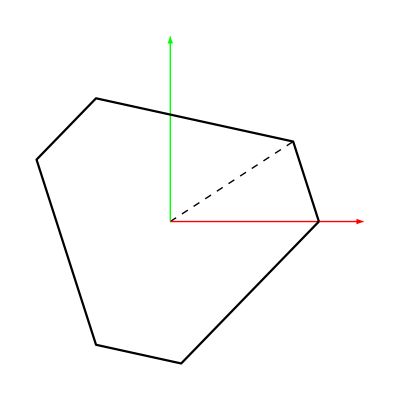

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (b/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

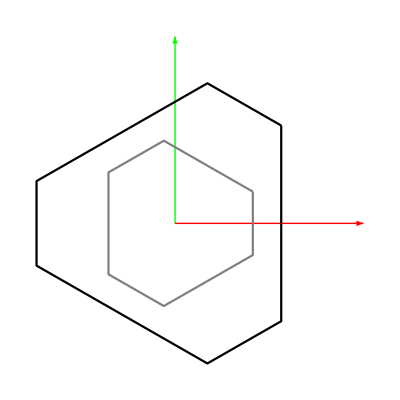

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
(*Locations of all the known ground joints*)
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;

tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];

b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];

al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
Show[Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Gray], AspectRatio->1, ImageResolution->600]
```

```mathematica
b/.datap
```

{{0.732576,0.680685,0},{0.223203,0.974772,0},{-0.955779,0.294087,0},{-0.955779,-0.294087,0},{0.223203,-0.974772,0},{0.732576,-0.680685,0}}

```mathematica
cords = {"x", "y", "z"};
```

```mathematica
acords = Table[Table[Symbol["a"<>ToString[j]<>cords[[i]]],{i, 3}],{j, 6}]
```

{{a1x,a1y,a1z},{a2x,a2y,a2z},{a3x,a3y,a3z},{a4x,a4y,a4z},{a5x,a5y,a5z},{a6x,a6y,a6z}}

```mathematica
Inner[Rule, Flatten[acords], Flatten[b/.datap], List]
```

{a1x→0.732576,a1y→0.680685,a1z→0,a2x→0.223203,a2y→0.974772,a2z→0,a3x→-0.955779,a3y→0.294087,a3z→0,a4x→-0.955779,a4y→-0.294087,a4z→0,a5x→0.223203,a5y→-0.974772,a5z→0,a6x→0.732576,a6y→-0.680685,a6z→0}

## Inverse Kinematics:

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
l= Table[Symbol["l"<>ToString[i]],{i, 6}];
(*a = Table[Symbol["a"<>ToString[i]],{i, 6}];*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
```

```mathematica
(*Considering ϕi, ψi and li's as the configuration space q*)
(*Rotation matrix of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
(*Angular velocity Jacobian of each leg*)
Jωl = Table[SkewMat2vec[Simplify[T[Rl[[i]]].D[Rl[[i]],{Join[ϕ,ψ, l]}]]],{i, 6}];
(*a in global frame via b*)
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*The mid point of the top platform will be*)
ptp = Total[a]/6;
```

```mathematica
(*(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a65 = Simplify[((a[[6]]-a[[5]])/Sqrt[((b[[6]]-b[[5]]).(b[[6]]-b[[5]]))/.rb->rt/.γb->γt])];
a15 = Simplify[((a[[1]]-a[[5]])/Sqrt[((b[[1]]-b[[5]]).(b[[1]]-b[[5]]))/.rb->rt/.γb->γt])];
(*a12 and a13 are unit vectors, but the cross need not be a unit vector and hence the Rotation matrix columns need to be re-normalised*)
(*We need to find the magnitude of the second and the third axes*)*)
```

```mathematica
(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a56 = Simplify[((a[[5]]-a[[6]])/Sqrt[((b[[5]]-b[[6]]).(b[[5]]-b[[6]]))/.rb->rt/.γb->γt])];
a16 = Simplify[((a[[1]]-a[[6]])/Sqrt[((b[[1]]-b[[6]]).(b[[1]]-b[[6]]))/.rb->rt/.γb->γt])];
```

```mathematica
(*sinangle = Simplify[(Cross[(b[[6]]-b[[5]])/Sqrt[(b[[6]]-b[[5]]).(b[[6]]-b[[5]])], (b[[1]]-b[[5]])/Sqrt[(b[[1]]-b[[5]]).(b[[1]]-b[[5]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a65, a15]/sinangle];
Rtp = {a65,  Cross[zaxis, a65], zaxis};*)
```

```mathematica
sinangle = Simplify[(Cross[(b[[1]]-b[[6]])/Sqrt[(b[[1]]-b[[6]]).(b[[1]]-b[[6]])], (b[[5]]-b[[6]])/Sqrt[(b[[5]]-b[[6]]).(b[[5]]-b[[6]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a16, a56]/sinangle];
Rtp = { Cross[a16, zaxis],a16, zaxis};
```

```mathematica
(*Now that we have obtained the rotation matrix, we can find the angular velocity Jacobian of the top plate*)
Jωt = SkewMat2vec[T[Rtp].D[Rtp,{Join[ϕ, ψ, l]}]];
```

```mathematica
(*CoM of the two parts of the prismatic joints*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {Join[ϕ, ψ, l]}];
Jpbi = D[pb, {Join[ϕ, ψ, l]}];
Jtp = D[ptp,  {Join[ϕ, ψ, l]}];
```

```mathematica
(*To generate the test data for this system*)
tpdat = {c1->0, c2->0, c3->0, x->0, y->0, z->1.1};
```

```mathematica
qrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
q = Join[ϕ, ψ, l]/.qrule;
```

```mathematica
Amat = vec2SkewMat[{c1, c2, c3}];
Rdat = Simplify[Inverse[(IdentityMatrix[3]-Amat)].(IdentityMatrix[3]+Amat)];
Simplify[Rdat.T[Rdat]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Rtps = Rtp/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.tpdat;
aldat = al/.datap;
ag =Simplify[Table[{x, y, z}+Rdat.aldat[[i]],{i, 6}]]/.tpdat;
bdat = b/.datap;
```

```mathematica
(*Formulating the constraint equations*)
```

```mathematica
η1 = Join[Simplify[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]]], {Simplify[Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])]], Simplify[Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])]], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
```

```mathematica
ηconfig = η1/.datap/.leglparam/.legmparam/.tpmparam/.qrule;
```

```mathematica
(*Therefore the sample solution satisfies the constraint equations*)
```

```mathematica
(*ηconfig/.datap/.leglparam/.legmparam/.tpmparam/.sampledat/.qrule*)
```

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}]; (*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]][t]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]][t]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]][t]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]][t]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
(*iksolver module*)
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp2.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp2 = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
pc = {x, y, z};
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp2.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating constraints in the extended configuration space*)
```

```mathematica
ηext = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
qx = {x, y, z, c1, c2, c3};
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{l1, _Complex},{l2, _Complex},{l3, _Complex},{l4, _Complex},{l5, _Complex},{l6, _Complex}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{ψ1, _Complex},{ψ2, _Complex},{ψ3, _Complex},{ψ4, _Complex},{ψ5, _Complex},{ψ6, _Complex}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksolC[x_] := Module[{lvals, ψvals, ϕvals, xrule, lrule, ψrule},
xrule = Inner[Rule, qx, x, List];
lvals = l/.lval/.xrule;
lrule = Inner[Rule, l, lvals, List];
ψvals = ψ/.ψval/.Join[xrule, lrule];
ψrule = Inner[Rule, ψ, ψvals, List];
ϕvals = ϕ/.ϕval/.Join[xrule,ψrule];
Return[Join[ϕvals, ψvals, lvals]]
]
```

```mathematica
(*verifying roots taken from Anirbans codes*)
```

```mathematica
roots = ({{x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
rootsC = ({{x->1.8700438348728161, y->-0.5235870043873335, z->0.-0.926898973258719 ⅈ, c1->0.-0.10569096861540776 ⅈ, c2->0.+0.7154784037290103 ⅈ, c3->0}, {x->1.8700438348728161, y->-0.5235870043873335, z->0.+0.926898973258719 ⅈ, c1->0.+0.10569096861540776 ⅈ, c2->0.-0.7154784037290103 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.-0.9685245785328371 ⅈ, c1->0.-0.6638886705593215 ⅈ, c2->0.-0.3422565386596551 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.+0.9685245785328371 ⅈ, c1->0.+0.6638886705593215 ⅈ, c2->0.+0.3422565386596551 ⅈ, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.-1.3894731322781502 ⅈ, c1->0.+0.6338547336758182 ⅈ, c2->0.-0.42758251604766423 ⅈ, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.+1.3894731322781502 ⅈ, c1->0.-0.6338547336758182 ⅈ, c2->0.+0.42758251604766423 ⅈ, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
ikroots = Table[Inner[Rule, Join[ϕ, ψ, l], iksolC[qx/.roots[[i]]], List], {i, Length[roots]}];
```

```mathematica
iksolC[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

```mathematica
initpose=Join[qx/.roots[[2]],iksolC[qx/.roots[[2]]]];
initposes=Table[Join[qx/.roots[[ii]],iksolC[qx/.roots[[ii]]]],{ii,8}];
initposeC = Join[qx/.rootsC[[1]],iksolC[qx/.rootsC[[1]]]];
```

```mathematica
xbrule = Table[{Symbol["xb"<>ToString[i]], Symbol["yb"<>ToString[i]], Symbol["zb"<>ToString[i]]},{i, 1, 6}];
xtrule = Table[{Symbol["xt"<>ToString[i]], Symbol["yt"<>ToString[i]], Symbol["zt"<>ToString[i]]},{i, 1, 6}];
```

```mathematica
top = Table[Inner[Rule, xtrule[[i]], (a/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xt1→0.628916,yt1→-0.430149,zt1→0.91962},{xt2→0.449784,yt2→-0.557918,zt2→0.245515},{xt3→0.127107,yt3→-0.844307,zt3→0.153522},{xt4→-0.212447,yt4→-1.17689,zt4→0.679753},{xt5→-0.101009,yt5→-1.09741,zt5→1.09912},{xt6→0.417678,yt6→-0.637052,zt6→1.24699}}

```mathematica
base = Table[Inner[Rule, xbrule[[i]], (b/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xb1→0.732576,yb1→0.680685,zb1→0},{xb2→0.223203,yb2→0.974772,zb2→0},{xb3→-0.955779,yb3→0.294087,zb3→0},{xb4→-0.955779,yb4→-0.294087,zb4→0},{xb5→0.223203,yb5→-0.974772,zb5→0},{xb6→0.732576,yb6→-0.680685,zb6→0}}

```mathematica
roots[[1]]
```

{x→0.218338,y→-0.790621,z→0.724086,c1→-0.715499,c2→-0.645258,c3→0}

```mathematica
Rationalize[base, 0.01]
```

{{xb1→8/11,yb1→11/16,zb1→0},{xb2→2/9,yb2→28/29,zb2→0},{xb3→-19/20,yb3→2/7,zb3→0},{xb4→-19/20,yb4→-2/7,zb4→0},{xb5→2/9,yb5→-29/30,zb5→0},{xb6→8/11,yb6→-13/19,zb6→0}}

```mathematica
Max[Table[ηconfig/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.ikroots[[i]], {i, Length[ikroots]}]];
```

```mathematica
roots//Dimensions
```

{8,6}

```mathematica
(*All the roots satisfy our constraint equation*)
```

```mathematica
(*{x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]}*)
```

## Compiled functions

```mathematica
cηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηconfig/.qrule], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηconfig = D[ηconfig/.qrule,{ q[[;;-7]]/.qrule}];
```

```mathematica
cJηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηconfig], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
cηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηext = D[ηext,{ Join[qx, q[[;;-7]]/.qrule]}];
```

```mathematica
Jηext//Variables
```

{c1,c2,c3,l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
cJηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

## Plotting the SRSPM:

```mathematica
qrule = Inner[Rule, q, Join[ϕ, ψ, l], List];
qvar = q/.qrule;
```

```mathematica
qfull = Join[qx, qvar];
```

```mathematica
(*Plotting SRSPM from discretisation starting position*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis]
]
```

```mathematica
(*Plotting the constraints*)
```

```mathematica
plotconstraints[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis, constraints, oval, pts},
oval=5;
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3/oval],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, 2,6}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85/oval],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, 2,6}];
(*Joints*)
jointsbase = Table[Graphics3D[{Opacity[1/oval],Sphere[bval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];
jointstop = Table[Graphics3D[{Opacity[1/oval],Sphere[aval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting constraints*)
constraints = Show[Graphics3D[{Gray,Arrowheads[0.04],Arrow[Tube[{{0,0,0},bval[[1]]},0.025]]}], Graphics3D[{Purple,Arrowheads[0.045],Arrow[Tube[{bval[[1]], (aval/.qvals)[[1]]},0.025]]}], Graphics3D[{Black,Arrowheads[0.045],Arrow[Tube[{(aval/.qvals)[[1]], {x,y,z}/.qvals},0.025]]}], Graphics3D[{Brown,Arrowheads[0.045],Arrow[Tube[{{0,0,0}, {x,y,z}/.qvals},0.025]]}]];
(*Mid points*)
pts = Show[Graphics3D[{Red, Opacity[0.5],Sphere[{0,0,0}, 0.06]}], Graphics3D[{Red, Opacity[0.5],Sphere[Mean[aval/.qvals], 0.06]}]];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis, constraints, pts]
]
```

```mathematica
pt = {0.2,0.2,1.1,0.1,0,0}
cpose = Inner[Rule, qfull,  Join[pt, iksolC[pt]], List];
plotconstraints[Chop[cpose]]
```

{0.2,0.2,1.1,0.1,0,0}

-Graphics3D-

```mathematica
plotsrspm[Chop[Inner[Rule, qfull, initpose, List]]]
```

-Graphics3D-

## Path generation

```mathematica
(*Select a circle, do the IK and get the values and fit a function to those leg values. Now track these functions with other initial conditions*)
```

```mathematica
scale = 0.2;
```

```mathematica
(* Circular path with changing orientation *)
(* parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*Cos[α], scale*Sin[α],scale*Sin[2*α]}; *)
```

```mathematica
(* Circular path with constant orientation *)
(* parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*1, scale*0,scale*0}; *)
```

```mathematica
(* Straight line path moving towards singularity *)
parampath = {scale-α,α, 1.28-α, scale*1, scale*0,scale*0};
```

```mathematica
pathpts = Table[parampath/.α->ii, {ii, 0, π/3, π/300}];
```

```mathematica
iksolC[pathpts[[1]]][[-6;;]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
pathplt=Graphics3D[{Red, Sphere[Chop[pathpts[[;;]]][[1;;77, ;;3]], 0.025]}];
```

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[pathpts[[u]], iksolC[pathpts[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[pathpts[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
(*Selected pose for plotting*)
```

```mathematica
(*plotsrspm[Inner[Rule, qfull, Join[pathpts[[43]], iksol[pathpts[[43]]]], List]]*)
```

```mathematica
(*get all the leg array for the circular motion*)
```

```mathematica
(*legvals = Table[Join[{i-1}, {iksol[pathpts[[i]]][[-6;;]]}], {i, Length[pathpts]}];*)
legvals = Table[iksolC[pathpts[[i]]][[-6;;]], {i, Length[pathpts]}];
```

```mathematica
legvals[[1]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
initpose=Join[pathpts[[1]], iksolC[pathpts[[1]]]]
```

{0.2,0,1.28,0.2,0.,0.,0.00305624-8.22748×10^-17 ⅈ,-0.0668855-2.77949×10^-17 ⅈ,0.456963-1.1835×10^-16 ⅈ,0.546956-1.39651×10^-17 ⅈ,-0.0946901-1.93388×10^-16 ⅈ,0.00349011-1.87171×10^-16 ⅈ,0.336276+1.47256×10^-17 ⅈ,0.286891-5.66207×10^-17 ⅈ,-0.0210274-2.43773×10^-17 ⅈ,0.0247844-1.74336×10^-16 ⅈ,-0.395383-1.37395×10^-16 ⅈ,-0.379795-1.10578×10^-16 ⅈ,1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
(*legvals//MatrixForm*)
(*legvals//Im//Flatten//CForm*)
```

```mathematica
(*legfunc = Interpolation[legvals]*)
```

## Newton-Raphson method for root tracking

### Real roots:

```mathematica
(*Now root tracking all the 8 solutions with this leg interpolation for the 50 points*)
```

```mathematica
(*Newton-Raphson method*)
```

```mathematica
NRTracking[thetai_, phii_, eta_, Jeta_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
(*Takes in eta and Jeta as compiled functions*)
nvec = eta@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[(Norm[nvec]≥ 10^-10)&&(loopcounter≤100),
loopcounter++;
Jmat =  Jeta@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = eta@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
(*Tracking using the extended configuration space*)
```

```mathematica
Jηext//Dimensions
Jηext//Variables
```

{18,18}

{c1,c2,c3,l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

### Root 1:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[1,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.54665×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[1,;;-7]];
tic[]
r1tempϕ = testext;
r1ϕlist = {r1tempϕ};
For[i=2,i≤Length[legvals], i++, 
r1tempϕ = NRTracking[legvals[[i]], r1tempϕ, cηext, cJηext];
AppendTo[r1ϕlist, r1tempϕ];
]
toc[]
```

Actual time consumed: 0.05248 seconds.

CPU time consumed: 0.052523 seconds.

```mathematica
r1xlist = r1ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r1trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r1xlist[[u]], iksolC[r1xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r1xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r1xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 2:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[2,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.54665×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[2,;;-7]];
tic[]
r2tempϕ = testext;
r2ϕlist = {r2tempϕ};
For[i=2,i≤89, i++, 
r2tempϕ = NRTracking[legvals[[i]], r2tempϕ, cηext, cJηext];
AppendTo[r2ϕlist, r2tempϕ];
]
toc[]
```

Actual time consumed: 0.06263 seconds.

CPU time consumed: 0.06264 seconds.

```mathematica
r2xlist = r2ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r2trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r2xlist[[u]], iksolC[r2xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r2xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r2xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 3:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[3,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.11426×10^-15

```mathematica
Length[legvals]
```

101

```mathematica
initposes[[3,;;-7]]
```

{-0.513695,-0.519996,-0.798723,-0.333759,-0.951699,0,-1.88547-1.05103×10^-16 ⅈ,-2.65366+2.74726×10^-17 ⅈ,2.78228+1.86009×10^-17 ⅈ,2.89251-1.51877×10^-16 ⅈ,-2.20522+5.34046×10^-17 ⅈ,-1.74294-1.42102×10^-16 ⅈ,0.61606-1.17742×10^-16 ⅈ,0.697469-2.13889×10^-16 ⅈ,0.419763+1.94314×10^-17 ⅈ,0.5377-1.52741×10^-16 ⅈ,0.0705025-6.62747×10^-17 ⅈ,-0.103948+3.0597×10^-18 ⅈ}

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[3,;;-7]];
tic[]
r3tempϕ = testext;
r3ϕlist = {r3tempϕ};
For[i=2,i≤89, i++, 
r3tempϕ = NRTracking[legvals[[i]], r3tempϕ, cηext, cJηext];
AppendTo[r3ϕlist, r3tempϕ];
]
toc[]
```

Actual time consumed: 0.03332 seconds.

CPU time consumed: 0.033447 seconds.

```mathematica
r3xlist = r3ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r3trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r3xlist[[u]], iksolC[r3xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r3xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r3xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 4:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[4,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.20587×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[4,;;-7]];
tic[]
r4tempϕ = testext;
r4ϕlist = {r4tempϕ};
For[i=2,i≤Length[legvals], i++, 
r4tempϕ = NRTracking[legvals[[i]], r4tempϕ, cηext, cJηext];
AppendTo[r4ϕlist, r4tempϕ];
]
toc[]
```

Actual time consumed: 0.05976 seconds.

CPU time consumed: 0.059812 seconds.

```mathematica
r4xlist//Chop//MatrixForm
```

(0.524434 | 0.268509 | 1.0308 | 0.603749 | -0.188561 | 0
0.509486 | 0.275006 | 1.02358 | 0.598574 | -0.186436 | 0
0.494536 | 0.281502 | 1.01637 | 0.593404 | -0.18431 | 0
0.479584 | 0.287998 | 1.00918 | 0.588241 | -0.182181 | 0
0.464632 | 0.294494 | 1.00199 | 0.583083 | -0.180051 | 0
0.449678 | 0.300991 | 0.994819 | 0.577931 | -0.177919 | 0
0.434724 | 0.307488 | 0.987658 | 0.572784 | -0.175784 | 0
0.419769 | 0.313987 | 0.980509 | 0.567642 | -0.173647 | 0
0.404813 | 0.320488 | 0.973371 | 0.562504 | -0.171508 | 0
0.389857 | 0.326991 | 0.966244 | 0.55737 | -0.169366 | 0
0.374902 | 0.333496 | 0.959128 | 0.55224 | -0.167221 | 0
0.359946 | 0.340003 | 0.952022 | 0.547114 | -0.165073 | 0
0.344991 | 0.346514 | 0.944928 | 0.541991 | -0.162921 | 0
0.330037 | 0.353029 | 0.937843 | 0.536871 | -0.160767 | 0
0.315084 | 0.359547 | 0.930769 | 0.531754 | -0.158608 | 0
0.300133 | 0.36607 | 0.923704 | 0.526639 | -0.156446 | 0
0.285182 | 0.372597 | 0.916649 | 0.521526 | -0.15428 | 0
0.270234 | 0.37913 | 0.909604 | 0.516414 | -0.15211 | 0
0.255288 | 0.385669 | 0.902567 | 0.511304 | -0.149935 | 0
0.240344 | 0.392214 | 0.89554 | 0.506195 | -0.147756 | 0
0.225402 | 0.398765 | 0.88852 | 0.501086 | -0.145572 | 0
0.210464 | 0.405324 | 0.881509 | 0.495978 | -0.143384 | 0
0.195529 | 0.41189 | 0.874506 | 0.490869 | -0.141189 | 0
0.180597 | 0.418464 | 0.86751 | 0.48576 | -0.13899 | 0
0.165669 | 0.425047 | 0.860522 | 0.480651 | -0.136784 | 0
0.150746 | 0.431639 | 0.85354 | 0.47554 | -0.134573 | 0
0.135827 | 0.43824 | 0.846564 | 0.470428 | -0.132356 | 0
0.120913 | 0.444852 | 0.839595 | 0.465313 | -0.130132 | 0
0.106004 | 0.451475 | 0.83263 | 0.460197 | -0.127901 | 0
0.0911 | 0.458109 | 0.825671 | 0.455078 | -0.125663 | 0
0.0762023 | 0.464755 | 0.818716 | 0.449955 | -0.123419 | 0
0.0613109 | 0.471413 | 0.811765 | 0.44483 | -0.121166 | 0
0.0464261 | 0.478085 | 0.804818 | 0.4397 | -0.118906 | 0
0.0315483 | 0.48477 | 0.797873 | 0.434566 | -0.116637 | 0
0.0166778 | 0.49147 | 0.79093 | 0.429427 | -0.11436 | 0
0.00181514 | 0.498185 | 0.783989 | 0.424283 | -0.112073 | 0
-0.0130394 | 0.504915 | 0.777048 | 0.419134 | -0.109778 | 0
-0.0278853 | 0.511662 | 0.770108 | 0.413978 | -0.107473 | 0
-0.0427222 | 0.518426 | 0.763167 | 0.408816 | -0.105158 | 0
-0.0575496 | 0.525208 | 0.756224 | 0.403647 | -0.102832 | 0
-0.0723672 | 0.532008 | 0.749279 | 0.39847 | -0.100496 | 0
-0.0871745 | 0.538828 | 0.742331 | 0.393285 | -0.098148 | 0
-0.101971 | 0.545667 | 0.735379 | 0.388092 | -0.0957883 | 0
-0.116756 | 0.552528 | 0.728421 | 0.38289 | -0.0934163 | 0
-0.13153 | 0.55941 | 0.721457 | 0.377678 | -0.0910314 | 0
-0.146291 | 0.566314 | 0.714486 | 0.372456 | -0.0886331 | 0
-0.161039 | 0.573242 | 0.707507 | 0.367224 | -0.0862207 | 0
-0.175775 | 0.580193 | 0.700517 | 0.36198 | -0.0837937 | 0
-0.190497 | 0.58717 | 0.693517 | 0.356724 | -0.0813512 | 0
-0.205204 | 0.594172 | 0.686504 | 0.351456 | -0.0788928 | 0
-0.219897 | 0.601201 | 0.679477 | 0.346175 | -0.0764174 | 0
-0.234574 | 0.608257 | 0.672435 | 0.340879 | -0.0739245 | 0
-0.249236 | 0.615342 | 0.665375 | 0.33557 | -0.071413 | 0
-0.263881 | 0.622457 | 0.658297 | 0.330245 | -0.068882 | 0
-0.278509 | 0.629602 | 0.651198 | 0.324904 | -0.0663305 | 0
-0.29312 | 0.636778 | 0.644076 | 0.319546 | -0.0637574 | 0
-0.307712 | 0.643986 | 0.636929 | 0.314171 | -0.0611615 | 0
-0.322286 | 0.651228 | 0.629755 | 0.308777 | -0.0585415 | 0
-0.336841 | 0.658504 | 0.622551 | 0.303364 | -0.055896 | 0
-0.351377 | 0.665815 | 0.615316 | 0.297931 | -0.0532235 | 0
-0.365892 | 0.673163 | 0.608045 | 0.292477 | -0.0505222 | 0
-0.380386 | 0.680548 | 0.600737 | 0.287001 | -0.0477902 | 0
-0.394859 | 0.687971 | 0.593388 | 0.281501 | -0.0450256 | 0
-0.40931 | 0.695433 | 0.585995 | 0.275977 | -0.042226 | 0
-0.423738 | 0.702936 | 0.578553 | 0.270428 | -0.0393888 | 0
-0.438144 | 0.71048 | 0.57106 | 0.264852 | -0.0365113 | 0
-0.452527 | 0.718067 | 0.563511 | 0.259248 | -0.03359 | 0
-0.466887 | 0.725696 | 0.555902 | 0.253614 | -0.0306215 | 0
-0.481223 | 0.733369 | 0.548227 | 0.247949 | -0.0276015 | 0
-0.495535 | 0.741087 | 0.540481 | 0.242252 | -0.0245252 | 0
-0.509823 | 0.748851 | 0.532658 | 0.23652 | -0.0213872 | 0
-0.524087 | 0.756659 | 0.524753 | 0.230753 | -0.018181 | 0
-0.538329 | 0.764514 | 0.516758 | 0.224946 | -0.0148992 | 0
-0.552547 | 0.772415 | 0.508665 | 0.2191 | -0.0115329 | 0
-0.566745 | 0.780362 | 0.500466 | 0.21321 | -0.00807154 | 0
-0.580922 | 0.788353 | 0.492152 | 0.207274 | -0.00450225 | 0
-0.595082 | 0.796387 | 0.483712 | 0.201289 | -0.000809406 | 0
-0.606342 | 0.806342 | 0.473658 | 0.2 | 0 | 0
-0.616814 | 0.816814 | 0.463186 | 0.2 | 0 | 0
-0.627286 | 0.827286 | 0.452714 | 0.2 | 0 | 0
-0.637758 | 0.837758 | 0.442242 | 0.2 | 0 | 0
-0.64823 | 0.84823 | 0.43177 | 0.2 | 0 | 0
-0.658702 | 0.858702 | 0.421298 | 0.2 | 0 | 0
-0.669174 | 0.869174 | 0.410826 | 0.2 | 0 | 0
-0.679646 | 0.879646 | 0.400354 | 0.2 | -2.62263×10^-10 | 0
-0.690118 | 0.890118 | 0.389882 | 0.2 | -1.09579×10^-10 | 0
-0.70059 | 0.90059 | 0.37941 | 0.2 | 0 | 0
-0.711062 | 0.911062 | 0.368938 | 0.2 | 0 | 0
-0.721534 | 0.921534 | 0.358466 | 0.2 | 0 | 0
-0.732006 | 0.932006 | 0.347994 | 0.2 | 0 | 0
-0.742478 | 0.942478 | 0.337522 | 0.2 | 0 | 0
-0.75295 | 0.95295 | 0.32705 | 0.2 | 0 | 0
-0.763422 | 0.963422 | 0.316578 | 0.2 | 0 | 0
-0.773894 | 0.973894 | 0.306106 | 0.2 | 0 | 0
-0.784366 | 0.984366 | 0.295634 | 0.2 | 0 | 0
-0.794838 | 0.994838 | 0.285162 | 0.2 | 0 | 0
-0.80531 | 1.00531 | 0.27469 | 0.2 | 0 | 0
-0.815782 | 1.01578 | 0.264218 | 0.2 | 0 | 0
-0.826254 | 1.02625 | 0.253746 | 0.2 | 0 | 0
-0.836726 | 1.03673 | 0.243274 | 0.2 | 0 | 0
-0.847198 | 1.0472 | 0.232802 | 0.2 | 0 | 0)

```mathematica
r4xlist = r4ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r4trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r4xlist[[u]], iksolC[r4xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r4xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r4xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 5:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[5,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

9.66454×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[5,;;-7]];
tic[]
r5tempϕ = testext;
r5ϕlist = {r5tempϕ};
For[i=2,i≤89, i++, 
r5tempϕ = NRTracking[legvals[[i]], r5tempϕ, cηext, cJηext];
AppendTo[r5ϕlist, r5tempϕ];
]
toc[]
```

Actual time consumed: 0.06321 seconds.

CPU time consumed: 0.063249 seconds.

```mathematica
r5xlist = r5ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r5trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r5xlist[[u]], iksolC[r5xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r5xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r5xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 6:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[6,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.097×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[6,;;-7]];
tic[]
r6tempϕ = testext;
r6ϕlist = {r6tempϕ};
For[i=2,i≤89, i++, 
r6tempϕ = NRTracking[legvals[[i]], r6tempϕ, cηext, cJηext];
AppendTo[r6ϕlist, r6tempϕ];
]
toc[]
```

Actual time consumed: 0.05674 seconds.

CPU time consumed: 0.056801 seconds.

```mathematica
r6xlist = r6ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r6trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r6xlist[[u]], iksolC[r6xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r6xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r6xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 7:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[7,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.47006×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[7,;;-7]];
tic[]
r7tempϕ = testext;
r7ϕlist = {r7tempϕ};
For[i=2,i≤Length[legvals], i++, 
r7tempϕ = NRTracking[legvals[[i]], r7tempϕ, cηext, cJηext];
AppendTo[r7ϕlist, r7tempϕ];
]
toc[]
```

Actual time consumed: 0.05464 seconds.

CPU time consumed: 0.054677 seconds.

```mathematica
r7xlist = r7ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r7trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r7xlist[[u]], iksolC[r7xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r7xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r7xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 8:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[8,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.28805×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[8,;;-7]];
tic[]
r8tempϕ = testext;
r8ϕlist = {r8tempϕ};
For[i=2,i≤Length[legvals], i++, 
r8tempϕ = NRTracking[legvals[[i]], r8tempϕ, cηext, cJηext];
AppendTo[r8ϕlist, r8tempϕ];
]
toc[]
```

Actual time consumed: 0.05735 seconds.

CPU time consumed: 0.057391 seconds.

```mathematica
r8xlist = r8ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r8trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r8xlist[[u]], iksolC[r8xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r8xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r8xlist], 1}]
```

```mathematica
r8xlist//Chop//MatrixForm
```

(0.524434 | 0.268509 | -1.0308 | -0.603749 | 0.188561 | 0
0.509486 | 0.275006 | -1.02358 | -0.598574 | 0.186436 | 0
0.494536 | 0.281502 | -1.01637 | -0.593404 | 0.18431 | 0
0.479584 | 0.287998 | -1.00918 | -0.588241 | 0.182181 | 0
0.464632 | 0.294494 | -1.00199 | -0.583083 | 0.180051 | 0
0.449678 | 0.300991 | -0.994819 | -0.577931 | 0.177919 | 0
0.434724 | 0.307488 | -0.987658 | -0.572784 | 0.175784 | 0
0.419769 | 0.313987 | -0.980509 | -0.567642 | 0.173647 | 0
0.404813 | 0.320488 | -0.973371 | -0.562504 | 0.171508 | 0
0.389857 | 0.326991 | -0.966244 | -0.55737 | 0.169366 | 0
0.374902 | 0.333496 | -0.959128 | -0.55224 | 0.167221 | 0
0.359946 | 0.340003 | -0.952022 | -0.547114 | 0.165073 | 0
0.344991 | 0.346514 | -0.944928 | -0.541991 | 0.162921 | 0
0.330037 | 0.353029 | -0.937843 | -0.536871 | 0.160767 | 0
0.315084 | 0.359547 | -0.930769 | -0.531754 | 0.158608 | 0
0.300133 | 0.36607 | -0.923704 | -0.526639 | 0.156446 | 0
0.285182 | 0.372597 | -0.916649 | -0.521526 | 0.15428 | 0
0.270234 | 0.37913 | -0.909604 | -0.516414 | 0.15211 | 0
0.255288 | 0.385669 | -0.902567 | -0.511304 | 0.149935 | 0
0.240344 | 0.392214 | -0.89554 | -0.506195 | 0.147756 | 0
0.225402 | 0.398765 | -0.88852 | -0.501086 | 0.145572 | 0
0.210464 | 0.405324 | -0.881509 | -0.495978 | 0.143384 | 0
0.195529 | 0.41189 | -0.874506 | -0.490869 | 0.141189 | 0
0.180597 | 0.418464 | -0.86751 | -0.48576 | 0.13899 | 0
0.165669 | 0.425047 | -0.860522 | -0.480651 | 0.136784 | 0
0.150746 | 0.431639 | -0.85354 | -0.47554 | 0.134573 | 0
0.135827 | 0.43824 | -0.846564 | -0.470428 | 0.132356 | 0
0.120913 | 0.444852 | -0.839595 | -0.465313 | 0.130132 | 0
0.106004 | 0.451475 | -0.83263 | -0.460197 | 0.127901 | 0
0.0911 | 0.458109 | -0.825671 | -0.455078 | 0.125663 | 0
0.0762023 | 0.464755 | -0.818716 | -0.449955 | 0.123419 | 0
0.0613109 | 0.471413 | -0.811765 | -0.44483 | 0.121166 | 0
0.0464261 | 0.478085 | -0.804818 | -0.4397 | 0.118906 | 0
0.0315483 | 0.48477 | -0.797873 | -0.434566 | 0.116637 | 0
0.0166778 | 0.49147 | -0.79093 | -0.429427 | 0.11436 | 0
0.00181514 | 0.498185 | -0.783989 | -0.424283 | 0.112073 | 0
-0.0130394 | 0.504915 | -0.777048 | -0.419134 | 0.109778 | 0
-0.0278853 | 0.511662 | -0.770108 | -0.413978 | 0.107473 | 0
-0.0427222 | 0.518426 | -0.763167 | -0.408816 | 0.105158 | 0
-0.0575496 | 0.525208 | -0.756224 | -0.403647 | 0.102832 | 0
-0.0723672 | 0.532008 | -0.749279 | -0.39847 | 0.100496 | 0
-0.0871745 | 0.538828 | -0.742331 | -0.393285 | 0.098148 | 0
-0.101971 | 0.545667 | -0.735379 | -0.388092 | 0.0957883 | 0
-0.116756 | 0.552528 | -0.728421 | -0.38289 | 0.0934163 | 0
-0.13153 | 0.55941 | -0.721457 | -0.377678 | 0.0910314 | 0
-0.146291 | 0.566314 | -0.714486 | -0.372456 | 0.0886331 | 0
-0.161039 | 0.573242 | -0.707507 | -0.367224 | 0.0862207 | 0
-0.175775 | 0.580193 | -0.700517 | -0.36198 | 0.0837937 | 0
-0.190497 | 0.58717 | -0.693517 | -0.356724 | 0.0813512 | 0
-0.205204 | 0.594172 | -0.686504 | -0.351456 | 0.0788928 | 0
-0.219897 | 0.601201 | -0.679477 | -0.346175 | 0.0764174 | 0
-0.234574 | 0.608257 | -0.672435 | -0.340879 | 0.0739245 | 0
-0.249236 | 0.615342 | -0.665375 | -0.33557 | 0.071413 | 0
-0.263881 | 0.622457 | -0.658297 | -0.330245 | 0.068882 | 0
-0.278509 | 0.629602 | -0.651198 | -0.324904 | 0.0663305 | 0
-0.29312 | 0.636778 | -0.644076 | -0.319546 | 0.0637574 | 0
-0.307712 | 0.643986 | -0.636929 | -0.314171 | 0.0611615 | 0
-0.322286 | 0.651228 | -0.629755 | -0.308777 | 0.0585415 | 0
-0.336841 | 0.658504 | -0.622551 | -0.303364 | 0.055896 | 0
-0.351377 | 0.665815 | -0.615316 | -0.297931 | 0.0532235 | 0
-0.365892 | 0.673163 | -0.608045 | -0.292477 | 0.0505222 | 0
-0.380386 | 0.680548 | -0.600737 | -0.287001 | 0.0477902 | 0
-0.394859 | 0.687971 | -0.593388 | -0.281501 | 0.0450256 | 0
-0.40931 | 0.695433 | -0.585995 | -0.275977 | 0.042226 | 0
-0.423738 | 0.702936 | -0.578553 | -0.270428 | 0.0393888 | 0
-0.438144 | 0.71048 | -0.57106 | -0.264852 | 0.0365113 | 0
-0.452527 | 0.718067 | -0.563511 | -0.259248 | 0.03359 | 0
-0.466887 | 0.725696 | -0.555902 | -0.253614 | 0.0306215 | 0
-0.481223 | 0.733369 | -0.548227 | -0.247949 | 0.0276015 | 0
-0.495535 | 0.741087 | -0.540481 | -0.242252 | 0.0245252 | 0
-0.509823 | 0.748851 | -0.532658 | -0.23652 | 0.0213872 | 0
-0.524087 | 0.756659 | -0.524753 | -0.230753 | 0.018181 | 0
-0.538329 | 0.764514 | -0.516758 | -0.224946 | 0.0148992 | 0
-0.552547 | 0.772415 | -0.508665 | -0.2191 | 0.0115329 | 0
-0.566745 | 0.780362 | -0.500466 | -0.21321 | 0.00807154 | 0
-0.580922 | 0.788353 | -0.492152 | -0.207274 | 0.00450225 | 0
-0.595082 | 0.796387 | -0.483712 | -0.201289 | 0.000809406 | 0
-0.606342 | 0.806342 | -0.473658 | -0.2 | 0 | 0
-0.616814 | 0.816814 | -0.463186 | -0.2 | 0 | 0
-0.627286 | 0.827286 | -0.452714 | -0.2 | 0 | 0
-0.637758 | 0.837758 | -0.442242 | -0.2 | 0 | 0
-0.64823 | 0.84823 | -0.43177 | -0.2 | 0 | 0
-0.658702 | 0.858702 | -0.421298 | -0.2 | 0 | 0
-0.669174 | 0.869174 | -0.410826 | -0.2 | 0 | 0
-0.679646 | 0.879646 | -0.400354 | -0.2 | 2.62263×10^-10 | 0
-0.690118 | 0.890118 | -0.389882 | -0.2 | 1.09578×10^-10 | 0
-0.70059 | 0.90059 | -0.37941 | -0.2 | 0 | 0
-0.711062 | 0.911062 | -0.368938 | -0.2 | 0 | 0
-0.721534 | 0.921534 | -0.358466 | -0.2 | 0 | 0
-0.732006 | 0.932006 | -0.347994 | -0.2 | 0 | 0
-0.742478 | 0.942478 | -0.337522 | -0.2 | 0 | 0
-0.75295 | 0.95295 | -0.32705 | -0.2 | 0 | 0
-0.763422 | 0.963422 | -0.316578 | -0.2 | 0 | 0
-0.773894 | 0.973894 | -0.306106 | -0.2 | 0 | 0
-0.784366 | 0.984366 | -0.295634 | -0.2 | 0 | 0
-0.794838 | 0.994838 | -0.285162 | -0.2 | 0 | 0
-0.80531 | 1.00531 | -0.27469 | -0.2 | 0 | 0
-0.815782 | 1.01578 | -0.264218 | -0.2 | 0 | 0
-0.826254 | 1.02625 | -0.253746 | -0.2 | 0 | 0
-0.836726 | 1.03673 | -0.243274 | -0.2 | 0 | 0
-0.847198 | 1.0472 | -0.232802 | -0.2 | 0 | 0)

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Observation: Comparing root 2 and root 4

```mathematica
Join[{{Iter,DetJηr2,DetJηr4,Text["Norm[r2-r4]"],r2,r2,r2,r2,r2,r2,r5,r5,r5,r5,r5,r5}},Table[Join[{ii,Det[cJηext@@Join[r2ϕlist[[ii]],legvals[[ii]]]],Det[cJηext@@Join[r4ϕlist[[ii]],legvals[[ii]]]],Norm[r2xlist[[ii]]-r4xlist[[ii]]]},r2xlist[[ii]],r4xlist[[ii]]],{ii,89}]]//Chop//MatrixForm
```

(Iter | DetJηr2 | DetJηr4 | Norm[r2-r4] | r2 | r2 | r2 | r2 | r2 | r2 | r5 | r5 | r5 | r5 | r5 | r5
1 | 31.9312 | -6.76838 | 0.661834 | 0.2 | 0 | 1.28 | 0.2 | 0 | 0 | 0.524434 | 0.268509 | 1.0308 | 0.603749 | -0.188561 | 0
2 | 29.4177 | -6.21885 | 0.65304 | 0.189528 | 0.010472 | 1.26953 | 0.2 | 0 | 0 | 0.509486 | 0.275006 | 1.02358 | 0.598574 | -0.186436 | 0
3 | 27.0901 | -5.71032 | 0.644244 | 0.179056 | 0.020944 | 1.25906 | 0.2 | 0 | 0 | 0.494536 | 0.281502 | 1.01637 | 0.593404 | -0.18431 | 0
4 | 24.9356 | -5.24025 | 0.635447 | 0.168584 | 0.0314159 | 1.24858 | 0.2 | 0 | 0 | 0.479584 | 0.287998 | 1.00918 | 0.588241 | -0.182181 | 0
5 | 22.9424 | -4.80622 | 0.626649 | 0.158112 | 0.0418879 | 1.23811 | 0.2 | 0 | 0 | 0.464632 | 0.294494 | 1.00199 | 0.583083 | -0.180051 | 0
6 | 21.0993 | -4.40591 | 0.617849 | 0.14764 | 0.0523599 | 1.22764 | 0.2 | 0 | 0 | 0.449678 | 0.300991 | 0.994819 | 0.577931 | -0.177919 | 0
7 | 19.3958 | -4.03712 | 0.609048 | 0.137168 | 0.0628319 | 1.21717 | 0.2 | 0 | 0 | 0.434724 | 0.307488 | 0.987658 | 0.572784 | -0.175784 | 0
8 | 17.8221 | -3.69776 | 0.600245 | 0.126696 | 0.0733038 | 1.2067 | 0.2 | 0 | 0 | 0.419769 | 0.313987 | 0.980509 | 0.567642 | -0.173647 | 0
9 | 16.3691 | -3.38584 | 0.591442 | 0.116224 | 0.0837758 | 1.19622 | 0.2 | 0 | 0 | 0.404813 | 0.320488 | 0.973371 | 0.562504 | -0.171508 | 0
10 | 15.028 | -3.09946 | 0.582638 | 0.105752 | 0.0942478 | 1.18575 | 0.2 | 0 | 0 | 0.389857 | 0.326991 | 0.966244 | 0.55737 | -0.169366 | 0
11 | 13.791 | -2.83685 | 0.573833 | 0.0952802 | 0.10472 | 1.17528 | 0.2 | 0 | 0 | 0.374902 | 0.333496 | 0.959128 | 0.55224 | -0.167221 | 0
12 | 12.6504 | -2.59629 | 0.565028 | 0.0848083 | 0.115192 | 1.16481 | 0.2 | 0 | 0 | 0.359946 | 0.340003 | 0.952022 | 0.547114 | -0.165073 | 0
13 | 11.5993 | -2.37618 | 0.556222 | 0.0743363 | 0.125664 | 1.15434 | 0.2 | 0 | 0 | 0.344991 | 0.346514 | 0.944928 | 0.541991 | -0.162921 | 0
14 | 10.6311 | -2.17501 | 0.547415 | 0.0638643 | 0.136136 | 1.14386 | 0.2 | 0 | 0 | 0.330037 | 0.353029 | 0.937843 | 0.536871 | -0.160767 | 0
15 | 9.73963 | -1.99133 | 0.538609 | 0.0533923 | 0.146608 | 1.13339 | 0.2 | 0 | 0 | 0.315084 | 0.359547 | 0.930769 | 0.531754 | -0.158608 | 0
16 | 8.91927 | -1.82381 | 0.529802 | 0.0429204 | 0.15708 | 1.12292 | 0.2 | 0 | 0 | 0.300133 | 0.36607 | 0.923704 | 0.526639 | -0.156446 | 0
17 | 8.16469 | -1.67115 | 0.520996 | 0.0324484 | 0.167552 | 1.11245 | 0.2 | 0 | 0 | 0.285182 | 0.372597 | 0.916649 | 0.521526 | -0.15428 | 0
18 | 7.47092 | -1.53216 | 0.51219 | 0.0219764 | 0.178024 | 1.10198 | 0.2 | 0 | 0 | 0.270234 | 0.37913 | 0.909604 | 0.516414 | -0.15211 | 0
19 | 6.83335 | -1.40571 | 0.503384 | 0.0115044 | 0.188496 | 1.0915 | 0.2 | 0 | 0 | 0.255288 | 0.385669 | 0.902567 | 0.511304 | -0.149935 | 0
20 | 6.2477 | -1.29074 | 0.494579 | 0.00103247 | 0.198968 | 1.08103 | 0.2 | 0 | 0 | 0.240344 | 0.392214 | 0.89554 | 0.506195 | -0.147756 | 0
21 | 5.70998 | -1.18626 | 0.485775 | -0.00943951 | 0.20944 | 1.07056 | 0.2 | 0 | 0 | 0.225402 | 0.398765 | 0.88852 | 0.501086 | -0.145572 | 0
22 | 5.21648 | -1.09134 | 0.476972 | -0.0199115 | 0.219911 | 1.06009 | 0.2 | 0 | 0 | 0.210464 | 0.405324 | 0.881509 | 0.495978 | -0.143384 | 0
23 | 4.76377 | -1.00512 | 0.468171 | -0.0303835 | 0.230383 | 1.04962 | 0.2 | 0 | 0 | 0.195529 | 0.41189 | 0.874506 | 0.490869 | -0.141189 | 0
24 | 4.34865 | -0.926788 | 0.459371 | -0.0408554 | 0.240855 | 1.03914 | 0.2 | 0 | 0 | 0.180597 | 0.418464 | 0.86751 | 0.48576 | -0.13899 | 0
25 | 3.96816 | -0.855605 | 0.450573 | -0.0513274 | 0.251327 | 1.02867 | 0.2 | 0 | 0 | 0.165669 | 0.425047 | 0.860522 | 0.480651 | -0.136784 | 0
26 | 3.61956 | -0.79088 | 0.441776 | -0.0617994 | 0.261799 | 1.0182 | 0.2 | 0 | 0 | 0.150746 | 0.431639 | 0.85354 | 0.47554 | -0.134573 | 0
27 | 3.3003 | -0.731977 | 0.432982 | -0.0722714 | 0.272271 | 1.00773 | 0.2 | 0 | 0 | 0.135827 | 0.43824 | 0.846564 | 0.470428 | -0.132356 | 0
28 | 3.00803 | -0.678312 | 0.424191 | -0.0827433 | 0.282743 | 0.997257 | 0.2 | 0 | 0 | 0.120913 | 0.444852 | 0.839595 | 0.465313 | -0.130132 | 0
29 | 2.74057 | -0.629354 | 0.415402 | -0.0932153 | 0.293215 | 0.986785 | 0.2 | 0 | 0 | 0.106004 | 0.451475 | 0.83263 | 0.460197 | -0.127901 | 0
30 | 2.4959 | -0.584618 | 0.406616 | -0.103687 | 0.303687 | 0.976313 | 0.2 | 0 | 0 | 0.0911 | 0.458109 | 0.825671 | 0.455078 | -0.125663 | 0
31 | 2.27218 | -0.543665 | 0.397834 | -0.114159 | 0.314159 | 0.965841 | 0.2 | 0 | 0 | 0.0762023 | 0.464755 | 0.818716 | 0.449955 | -0.123419 | 0
32 | 2.06768 | -0.5061 | 0.389055 | -0.124631 | 0.324631 | 0.955369 | 0.2 | 0 | 0 | 0.0613109 | 0.471413 | 0.811765 | 0.44483 | -0.121166 | 0
33 | 1.88081 | -0.471567 | 0.380281 | -0.135103 | 0.335103 | 0.944897 | 0.2 | 0 | 0 | 0.0464261 | 0.478085 | 0.804818 | 0.4397 | -0.118906 | 0
34 | 1.71012 | -0.43975 | 0.37151 | -0.145575 | 0.345575 | 0.934425 | 0.2 | 0 | 0 | 0.0315483 | 0.48477 | 0.797873 | 0.434566 | -0.116637 | 0
35 | 1.55425 | -0.410367 | 0.362744 | -0.156047 | 0.356047 | 0.923953 | 0.2 | 0 | 0 | 0.0166778 | 0.49147 | 0.79093 | 0.429427 | -0.11436 | 0
36 | 1.41196 | -0.383166 | 0.353983 | -0.166519 | 0.366519 | 0.913481 | 0.2 | 0 | 0 | 0.00181514 | 0.498185 | 0.783989 | 0.424283 | -0.112073 | 0
37 | 1.28212 | -0.357928 | 0.345227 | -0.176991 | 0.376991 | 0.903009 | 0.2 | 0 | 0 | -0.0130394 | 0.504915 | 0.777048 | 0.419134 | -0.109778 | 0
38 | 1.16366 | -0.334457 | 0.336477 | -0.187463 | 0.387463 | 0.892537 | 0.2 | 0 | 0 | -0.0278853 | 0.511662 | 0.770108 | 0.413978 | -0.107473 | 0
39 | 1.05563 | -0.312582 | 0.327732 | -0.197935 | 0.397935 | 0.882065 | 0.2 | 0 | 0 | -0.0427222 | 0.518426 | 0.763167 | 0.408816 | -0.105158 | 0
40 | 0.957136 | -0.292153 | 0.318994 | -0.208407 | 0.408407 | 0.871593 | 0.2 | 0 | 0 | -0.0575496 | 0.525208 | 0.756224 | 0.403647 | -0.102832 | 0
41 | 0.867359 | -0.273039 | 0.310262 | -0.218879 | 0.418879 | 0.861121 | 0.2 | 0 | 0 | -0.0723672 | 0.532008 | 0.749279 | 0.39847 | -0.100496 | 0
42 | 0.785552 | -0.255124 | 0.301537 | -0.229351 | 0.429351 | 0.850649 | 0.2 | 0 | 0 | -0.0871745 | 0.538828 | 0.742331 | 0.393285 | -0.098148 | 0
43 | 0.711029 | -0.238309 | 0.292819 | -0.239823 | 0.439823 | 0.840177 | 0.2 | 0 | 0 | -0.101971 | 0.545667 | 0.735379 | 0.388092 | -0.0957883 | 0
44 | 0.643158 | -0.222505 | 0.284109 | -0.250295 | 0.450295 | 0.829705 | 0.2 | 0 | 0 | -0.116756 | 0.552528 | 0.728421 | 0.38289 | -0.0934163 | 0
45 | 0.581364 | -0.207635 | 0.275407 | -0.260767 | 0.460767 | 0.819233 | 0.2 | 0 | 0 | -0.13153 | 0.55941 | 0.721457 | 0.377678 | -0.0910314 | 0
46 | 0.525117 | -0.19363 | 0.266713 | -0.271239 | 0.471239 | 0.808761 | 0.2 | 0 | 0 | -0.146291 | 0.566314 | 0.714486 | 0.372456 | -0.0886331 | 0
47 | 0.473933 | -0.180431 | 0.258029 | -0.281711 | 0.481711 | 0.798289 | 0.2 | 0 | 0 | -0.161039 | 0.573242 | 0.707507 | 0.367224 | -0.0862207 | 0
48 | 0.427369 | -0.167984 | 0.249353 | -0.292183 | 0.492183 | 0.787817 | 0.2 | 0 | 0 | -0.175775 | 0.580193 | 0.700517 | 0.36198 | -0.0837937 | 0
49 | 0.38502 | -0.156243 | 0.240686 | -0.302655 | 0.502655 | 0.777345 | 0.2 | 0 | 0 | -0.190497 | 0.58717 | 0.693517 | 0.356724 | -0.0813512 | 0
50 | 0.346516 | -0.145164 | 0.23203 | -0.313127 | 0.513127 | 0.766873 | 0.2 | 0 | 0 | -0.205204 | 0.594172 | 0.686504 | 0.351456 | -0.0788928 | 0
51 | 0.311518 | -0.134709 | 0.223383 | -0.323599 | 0.523599 | 0.756401 | 0.2 | 0 | 0 | -0.219897 | 0.601201 | 0.679477 | 0.346175 | -0.0764174 | 0
52 | 0.279718 | -0.124845 | 0.214748 | -0.334071 | 0.534071 | 0.745929 | 0.2 | 0 | 0 | -0.234574 | 0.608257 | 0.672435 | 0.340879 | -0.0739245 | 0
53 | 0.250831 | -0.115539 | 0.206122 | -0.344543 | 0.544543 | 0.735457 | 0.2 | 0 | 0 | -0.249236 | 0.615342 | 0.665375 | 0.33557 | -0.071413 | 0
54 | 0.224601 | -0.106762 | 0.197508 | -0.355015 | 0.555015 | 0.724985 | 0.2 | 0 | 0 | -0.263881 | 0.622457 | 0.658297 | 0.330245 | -0.068882 | 0
55 | 0.200793 | -0.0984867 | 0.188906 | -0.365487 | 0.565487 | 0.714513 | 0.2 | 0 | 0 | -0.278509 | 0.629602 | 0.651198 | 0.324904 | -0.0663305 | 0
56 | 0.179191 | -0.0906882 | 0.180315 | -0.375959 | 0.575959 | 0.704041 | 0.2 | 0 | 0 | -0.29312 | 0.636778 | 0.644076 | 0.319546 | -0.0637574 | 0
57 | 0.1596 | -0.0833423 | 0.171735 | -0.386431 | 0.586431 | 0.693569 | 0.2 | 0 | 0 | -0.307712 | 0.643986 | 0.636929 | 0.314171 | -0.0611615 | 0
58 | 0.141841 | -0.076426 | 0.163168 | -0.396903 | 0.596903 | 0.683097 | 0.2 | 0 | 0 | -0.322286 | 0.651228 | 0.629755 | 0.308777 | -0.0585415 | 0
59 | 0.12575 | -0.0699173 | 0.154613 | -0.407375 | 0.607375 | 0.672625 | 0.2 | 0 | 0 | -0.336841 | 0.658504 | 0.622551 | 0.303364 | -0.055896 | 0
60 | 0.11118 | -0.0637949 | 0.146069 | -0.417847 | 0.617847 | 0.662153 | 0.2 | 0 | 0 | -0.351377 | 0.665815 | 0.615316 | 0.297931 | -0.0532235 | 0
61 | 0.0979951 | -0.058038 | 0.137538 | -0.428319 | 0.628319 | 0.651681 | 0.2 | 0 | 0 | -0.365892 | 0.673163 | 0.608045 | 0.292477 | -0.0505222 | 0
62 | 0.0860706 | -0.0526262 | 0.129019 | -0.438791 | 0.638791 | 0.641209 | 0.2 | 0 | 0 | -0.380386 | 0.680548 | 0.600737 | 0.287001 | -0.0477902 | 0
63 | 0.0752941 | -0.0475395 | 0.120511 | -0.449262 | 0.649262 | 0.630738 | 0.2 | 0 | 0 | -0.394859 | 0.687971 | 0.593388 | 0.281501 | -0.0450256 | 0
64 | 0.0655625 | -0.0427582 | 0.112014 | -0.459734 | 0.659734 | 0.620266 | 0.2 | 0 | 0 | -0.40931 | 0.695433 | 0.585995 | 0.275977 | -0.042226 | 0
65 | 0.0567818 | -0.0382629 | 0.103528 | -0.470206 | 0.670206 | 0.609794 | 0.2 | 0 | 0 | -0.423738 | 0.702936 | 0.578553 | 0.270428 | -0.0393888 | 0
66 | 0.0488659 | -0.0340345 | 0.0950518 | -0.480678 | 0.680678 | 0.599322 | 0.2 | 0 | 0 | -0.438144 | 0.71048 | 0.57106 | 0.264852 | -0.0365113 | 0
67 | 0.0417364 | -0.0300544 | 0.0865843 | -0.49115 | 0.69115 | 0.58885 | 0.2 | 0 | 0 | -0.452527 | 0.718067 | 0.563511 | 0.259248 | -0.03359 | 0
68 | 0.0353213 | -0.0263045 | 0.0781244 | -0.501622 | 0.701622 | 0.578378 | 0.2 | 0 | 0 | -0.466887 | 0.725696 | 0.555902 | 0.253614 | -0.0306215 | 0
69 | 0.0295549 | -0.0227676 | 0.0696703 | -0.512094 | 0.712094 | 0.567906 | 0.2 | 0 | 0 | -0.481223 | 0.733369 | 0.548227 | 0.247949 | -0.0276015 | 0
70 | 0.0243768 | -0.019427 | 0.0612199 | -0.522566 | 0.722566 | 0.557434 | 0.2 | 2.14691×10^-10 | 0 | -0.495535 | 0.741087 | 0.540481 | 0.242252 | -0.0245252 | 0
71 | 0.0197318 | -0.0162676 | 0.0527706 | -0.533038 | 0.733038 | 0.546962 | 0.2 | 0 | 0 | -0.509823 | 0.748851 | 0.532658 | 0.23652 | -0.0213872 | 0
72 | 0.0155691 | -0.0132754 | 0.044319 | -0.54351 | 0.74351 | 0.53649 | 0.2 | 0 | 0 | -0.524087 | 0.756659 | 0.524753 | 0.230753 | -0.018181 | 0
73 | 0.0118419 | -0.0104382 | 0.0358611 | -0.553982 | 0.753982 | 0.526018 | 0.2 | 0 | 0 | -0.538329 | 0.764514 | 0.516758 | 0.224946 | -0.0148992 | 0
74 | 0.00850733 | -0.00774596 | 0.0273915 | -0.564454 | 0.764454 | 0.515546 | 0.2 | 0 | 0 | -0.552547 | 0.772415 | 0.508665 | 0.2191 | -0.0115329 | 0
75 | 0.00552563 | -0.00519075 | 0.0189039 | -0.574926 | 0.774926 | 0.505074 | 0.2 | 0 | 0 | -0.566745 | 0.780362 | 0.500466 | 0.21321 | -0.00807154 | 0
76 | 0.00286018 | -0.00276755 | 0.0103899 | -0.585398 | 0.785398 | 0.494602 | 0.2 | 0 | 0 | -0.580922 | 0.788353 | 0.492152 | 0.207274 | -0.00450225 | 0
77 | 0.00047711 | -0.000474483 | 0.00183891 | -0.59587 | 0.79587 | 0.48413 | 0.2 | 1.70191×10^-9 | 0 | -0.595082 | 0.796387 | 0.483712 | 0.201289 | -0.000809406 | 0
78 | 0.00168674 | -0.00165499 | 0.00676267 | -0.609227 | 0.804462 | 0.475134 | 0.195252 | 0.00302648 | 0 | -0.606342 | 0.806342 | 0.473658 | 0.2 | 0 | 0
79 | 0.00371013 | -0.00356522 | 0.0154327 | -0.623362 | 0.812575 | 0.466405 | 0.189159 | 0.00703003 | 0 | -0.616814 | 0.816814 | 0.463186 | 0.2 | 0 | 0
80 | 0.00558469 | -0.00528062 | 0.0241948 | -0.637494 | 0.820719 | 0.45751 | 0.183004 | 0.0112331 | 0 | -0.627286 | 0.827286 | 0.452714 | 0.2 | 0 | 0
81 | 0.00729319 | -0.00682629 | 0.0330813 | -0.651631 | 0.828885 | 0.448431 | 0.176782 | 0.0156777 | 0 | -0.637758 | 0.837758 | 0.442242 | 0.2 | 0 | 0
82 | 0.00881038 | -0.00822561 | 0.0421373 | -0.665787 | 0.837063 | 0.439147 | 0.170485 | 0.0204214 | 0 | -0.64823 | 0.84823 | 0.43177 | 0.2 | 0 | 0
83 | 0.0100998 | -0.00950029 | 0.0514287 | -0.679983 | 0.84523 | 0.429633 | 0.164105 | 0.0255458 | 0 | -0.658702 | 0.858702 | 0.421298 | 0.2 | 0 | 0
84 | 0.0111078 | -0.0106705 | 0.0610556 | -0.69425 | 0.853357 | 0.419857 | 0.157627 | 0.0311728 | 0 | -0.669174 | 0.869174 | 0.410826 | 0.2 | 0 | 0
85 | 0.0117513 | -0.0117551 | 0.0711827 | -0.708644 | 0.861387 | 0.409778 | 0.151033 | 0.0374978 | 0 | -0.679646 | 0.879646 | 0.400354 | 0.2 | -2.62263×10^-10 | 0
86 | 0.0118873 | -0.0127716 | 0.0821097 | -0.723265 | 0.869217 | 0.399336 | 0.144287 | 0.0448684 | 0 | -0.690118 | 0.890118 | 0.389882 | 0.2 | -1.09579×10^-10 | 0
87 | 0.0112204 | -0.0137361 | 0.0944865 | -0.738338 | 0.876617 | 0.388431 | 0.13732 | 0.0540185 | 0 | -0.70059 | 0.90059 | 0.37941 | 0.2 | 0 | 0
88 | 0.00884884 | -0.0146638 | 0.110351 | -0.754579 | 0.882846 | 0.376815 | 0.129912 | 0.0671788 | 0 | -0.711062 | 0.911062 | 0.368938 | 0.2 | 0 | 0
89 | 0.00708378 | -0.0155688 | 0.117879 | -0.767331 | 0.892722 | 0.365674 | 0.12355 | 0.071214 | 9.42933×10^-7 | -0.721534 | 0.921534 | 0.358466 | 0.2 | 0 | 0)

### Observation: Comparing root 5 and root 8

```mathematica
Join[{{Iter,DetJηr5,DetJηr8,Text["Norm[r5-r8]"],r5,r5,r5,r5,r5,r5,r8,r8,r8,r8,r8,r8}},Table[Join[{ii,Det[cJηext@@Join[r5ϕlist[[ii]],legvals[[ii]]]],Det[cJηext@@Join[r8ϕlist[[ii]],legvals[[ii]]]],Norm[r5xlist[[ii]]-r8xlist[[ii]]]},r6xlist[[ii]],r8xlist[[ii]]],{ii,89}]]//Chop//MatrixForm
```

(Iter | DetJηr5 | DetJηr8 | Norm[r5-r8] | r5 | r5 | r5 | r5 | r5 | r5 | r8 | r8 | r8 | r8 | r8 | r8
1 | -31.9312 | 6.76838 | 0.661834 | -0.513695 | -0.519996 | 0.798723 | 0.333759 | 0.951699 | 0 | 0.524434 | 0.268509 | -1.0308 | -0.603749 | 0.188561 | 0
2 | -29.4177 | 6.21885 | 0.65304 | -0.514514 | -0.504379 | 0.793424 | 0.33059 | 0.938983 | 0 | 0.509486 | 0.275006 | -1.02358 | -0.598574 | 0.186436 | 0
3 | -27.0901 | 5.71032 | 0.644244 | -0.515349 | -0.488762 | 0.788178 | 0.327478 | 0.926446 | 0 | 0.494536 | 0.281502 | -1.01637 | -0.593404 | 0.18431 | 0
4 | -24.9356 | 5.24025 | 0.635447 | -0.516204 | -0.473144 | 0.782983 | 0.32442 | 0.914082 | 0 | 0.479584 | 0.287998 | -1.00918 | -0.588241 | 0.182181 | 0
5 | -22.9424 | 4.80622 | 0.626649 | -0.51708 | -0.457526 | 0.77784 | 0.321414 | 0.901887 | 0 | 0.464632 | 0.294494 | -1.00199 | -0.583083 | 0.180051 | 0
6 | -21.0993 | 4.40591 | 0.617849 | -0.517977 | -0.441907 | 0.772749 | 0.318458 | 0.889856 | 0 | 0.449678 | 0.300991 | -0.994819 | -0.577931 | 0.177919 | 0
7 | -19.3958 | 4.03712 | 0.609048 | -0.518898 | -0.426288 | 0.767707 | 0.315551 | 0.877984 | 0 | 0.434724 | 0.307488 | -0.987658 | -0.572784 | 0.175784 | 0
8 | -17.8221 | 3.69776 | 0.600245 | -0.519844 | -0.410668 | 0.762715 | 0.312692 | 0.866265 | 0 | 0.419769 | 0.313987 | -0.980509 | -0.567642 | 0.173647 | 0
9 | -16.3691 | 3.38584 | 0.591442 | -0.520817 | -0.395048 | 0.757772 | 0.309878 | 0.854696 | 0 | 0.404813 | 0.320488 | -0.973371 | -0.562504 | 0.171508 | 0
10 | -15.028 | 3.09946 | 0.582638 | -0.521818 | -0.379427 | 0.752877 | 0.307108 | 0.843273 | 0 | 0.389857 | 0.326991 | -0.966244 | -0.55737 | 0.169366 | 0
11 | -13.791 | 2.83685 | 0.573833 | -0.522849 | -0.363804 | 0.748029 | 0.30438 | 0.831991 | 0 | 0.374902 | 0.333496 | -0.959128 | -0.55224 | 0.167221 | 0
12 | -12.6504 | 2.59629 | 0.565028 | -0.523911 | -0.348181 | 0.743228 | 0.301694 | 0.820845 | 0 | 0.359946 | 0.340003 | -0.952022 | -0.547114 | 0.165073 | 0
13 | -11.5993 | 2.37618 | 0.556222 | -0.525006 | -0.332557 | 0.738473 | 0.299047 | 0.809833 | 0 | 0.344991 | 0.346514 | -0.944928 | -0.541991 | 0.162921 | 0
14 | -10.6311 | 2.17501 | 0.547415 | -0.526135 | -0.316932 | 0.733762 | 0.296438 | 0.79895 | 0 | 0.330037 | 0.353029 | -0.937843 | -0.536871 | 0.160767 | 0
15 | -9.73963 | 1.99133 | 0.538609 | -0.527299 | -0.301306 | 0.729096 | 0.293866 | 0.788193 | 0 | 0.315084 | 0.359547 | -0.930769 | -0.531754 | 0.158608 | 0
16 | -8.91927 | 1.82381 | 0.529802 | -0.5285 | -0.285678 | 0.724473 | 0.291329 | 0.777558 | 0 | 0.300133 | 0.36607 | -0.923704 | -0.526639 | 0.156446 | 0
17 | -8.16469 | 1.67115 | 0.520996 | -0.52974 | -0.27005 | 0.719892 | 0.288826 | 0.767042 | 0 | 0.285182 | 0.372597 | -0.916649 | -0.521526 | 0.15428 | 0
18 | -7.47092 | 1.53216 | 0.51219 | -0.531019 | -0.254419 | 0.715352 | 0.286357 | 0.756641 | 0 | 0.270234 | 0.37913 | -0.909604 | -0.516414 | 0.15211 | 0
19 | -6.83335 | 1.40571 | 0.503384 | -0.53234 | -0.238788 | 0.710852 | 0.283918 | 0.746353 | 0 | 0.255288 | 0.385669 | -0.902567 | -0.511304 | 0.149935 | 0
20 | -6.2477 | 1.29074 | 0.494579 | -0.533704 | -0.223155 | 0.706391 | 0.28151 | 0.736173 | 0 | 0.240344 | 0.392214 | -0.89554 | -0.506195 | 0.147756 | 0
21 | -5.70998 | 1.18626 | 0.485775 | -0.535111 | -0.20752 | 0.701968 | 0.279132 | 0.726099 | 0 | 0.225402 | 0.398765 | -0.88852 | -0.501086 | 0.145572 | 0
22 | -5.21648 | 1.09134 | 0.476972 | -0.536564 | -0.191883 | 0.697583 | 0.276781 | 0.716128 | 0 | 0.210464 | 0.405324 | -0.881509 | -0.495978 | 0.143384 | 0
23 | -4.76377 | 1.00512 | 0.468171 | -0.538063 | -0.176245 | 0.693232 | 0.274457 | 0.706257 | 0 | 0.195529 | 0.41189 | -0.874506 | -0.490869 | 0.141189 | 0
24 | -4.34865 | 0.926788 | 0.459371 | -0.53961 | -0.160605 | 0.688916 | 0.272159 | 0.696483 | 0 | 0.180597 | 0.418464 | -0.86751 | -0.48576 | 0.13899 | 0
25 | -3.96816 | 0.855605 | 0.450573 | -0.541207 | -0.144963 | 0.684634 | 0.269885 | 0.686803 | 0 | 0.165669 | 0.425047 | -0.860522 | -0.480651 | 0.136784 | 0
26 | -3.61956 | 0.79088 | 0.441776 | -0.542854 | -0.129318 | 0.680383 | 0.267635 | 0.677215 | 0 | 0.150746 | 0.431639 | -0.85354 | -0.47554 | 0.134573 | 0
27 | -3.3003 | 0.731977 | 0.432982 | -0.544554 | -0.113672 | 0.676163 | 0.265407 | 0.667717 | 0 | 0.135827 | 0.43824 | -0.846564 | -0.470428 | 0.132356 | 0
28 | -3.00803 | 0.678312 | 0.424191 | -0.546306 | -0.0980228 | 0.671971 | 0.2632 | 0.658304 | 0 | 0.120913 | 0.444852 | -0.839595 | -0.465313 | 0.130132 | 0
29 | -2.74057 | 0.629354 | 0.415402 | -0.548113 | -0.0823714 | 0.667808 | 0.261014 | 0.648976 | 0 | 0.106004 | 0.451475 | -0.83263 | -0.460197 | 0.127901 | 0
30 | -2.4959 | 0.584618 | 0.406616 | -0.549975 | -0.0667174 | 0.66367 | 0.258846 | 0.639729 | 0 | 0.0911 | 0.458109 | -0.825671 | -0.455078 | 0.125663 | 0
31 | -2.27218 | 0.543665 | 0.397834 | -0.551894 | -0.0510607 | 0.659557 | 0.256697 | 0.630561 | 0 | 0.0762023 | 0.464755 | -0.818716 | -0.449955 | 0.123419 | 0
32 | -2.06768 | 0.5061 | 0.389055 | -0.553871 | -0.0354012 | 0.655467 | 0.254564 | 0.621469 | 0 | 0.0613109 | 0.471413 | -0.811765 | -0.44483 | 0.121166 | 0
33 | -1.88081 | 0.471567 | 0.380281 | -0.555908 | -0.0197387 | 0.651399 | 0.252448 | 0.612452 | 0 | 0.0464261 | 0.478085 | -0.804818 | -0.4397 | 0.118906 | 0
34 | -1.71012 | 0.43975 | 0.37151 | -0.558004 | -0.00407311 | 0.64735 | 0.250346 | 0.603506 | 0 | 0.0315483 | 0.48477 | -0.797873 | -0.434566 | 0.116637 | 0
35 | -1.55425 | 0.410367 | 0.362744 | -0.560162 | 0.0115958 | 0.643319 | 0.248259 | 0.59463 | 0 | 0.0166778 | 0.49147 | -0.79093 | -0.429427 | 0.11436 | 0
36 | -1.41196 | 0.383166 | 0.353983 | -0.562382 | 0.027268 | 0.639304 | 0.246184 | 0.585821 | 0 | 0.00181514 | 0.498185 | -0.783989 | -0.424283 | 0.112073 | 0
37 | -1.28212 | 0.357928 | 0.345227 | -0.564666 | 0.0429439 | 0.635304 | 0.24412 | 0.577077 | 0 | -0.0130394 | 0.504915 | -0.777048 | -0.419134 | 0.109778 | 0
38 | -1.16366 | 0.334457 | 0.336477 | -0.567015 | 0.0586235 | 0.631315 | 0.242068 | 0.568396 | 0 | -0.0278853 | 0.511662 | -0.770108 | -0.413978 | 0.107473 | 0
39 | -1.05563 | 0.312582 | 0.327732 | -0.569429 | 0.074307 | 0.627337 | 0.240025 | 0.559776 | 0 | -0.0427222 | 0.518426 | -0.763167 | -0.408816 | 0.105158 | 0
40 | -0.957136 | 0.292153 | 0.318994 | -0.57191 | 0.0899946 | 0.623367 | 0.237991 | 0.551214 | 0 | -0.0575496 | 0.525208 | -0.756224 | -0.403647 | 0.102832 | 0
41 | -0.867359 | 0.273039 | 0.310262 | -0.574459 | 0.105686 | 0.619402 | 0.235965 | 0.542707 | 0 | -0.0723672 | 0.532008 | -0.749279 | -0.39847 | 0.100496 | 0
42 | -0.785552 | 0.255124 | 0.301537 | -0.577076 | 0.121383 | 0.615442 | 0.233945 | 0.534255 | 0 | -0.0871745 | 0.538828 | -0.742331 | -0.393285 | 0.098148 | 0
43 | -0.711029 | 0.238309 | 0.292819 | -0.579763 | 0.137084 | 0.611483 | 0.23193 | 0.525854 | 0 | -0.101971 | 0.545667 | -0.735379 | -0.388092 | 0.0957883 | 0
44 | -0.643158 | 0.222505 | 0.284109 | -0.582521 | 0.15279 | 0.607523 | 0.22992 | 0.517503 | 0 | -0.116756 | 0.552528 | -0.728421 | -0.38289 | 0.0934163 | 0
45 | -0.581364 | 0.207635 | 0.275407 | -0.585349 | 0.168501 | 0.60356 | 0.227913 | 0.509199 | 0 | -0.13153 | 0.55941 | -0.721457 | -0.377678 | 0.0910314 | 0
46 | -0.525117 | 0.19363 | 0.266713 | -0.58825 | 0.184217 | 0.599591 | 0.225909 | 0.500939 | 0 | -0.146291 | 0.566314 | -0.714486 | -0.372456 | 0.0886331 | 0
47 | -0.473933 | 0.180431 | 0.258029 | -0.591224 | 0.199939 | 0.595614 | 0.223905 | 0.492722 | 0 | -0.161039 | 0.573242 | -0.707507 | -0.367224 | 0.0862207 | 0
48 | -0.427369 | 0.167984 | 0.249353 | -0.594272 | 0.215667 | 0.591625 | 0.221901 | 0.484546 | 0 | -0.175775 | 0.580193 | -0.700517 | -0.36198 | 0.0837937 | 0
49 | -0.38502 | 0.156243 | 0.240686 | -0.597395 | 0.2314 | 0.587622 | 0.219896 | 0.476407 | 0 | -0.190497 | 0.58717 | -0.693517 | -0.356724 | 0.0813512 | 0
50 | -0.346516 | 0.145164 | 0.23203 | -0.600592 | 0.247141 | 0.583602 | 0.217888 | 0.468304 | 0 | -0.205204 | 0.594172 | -0.686504 | -0.351456 | 0.0788928 | 0
51 | -0.311518 | 0.134709 | 0.223383 | -0.603866 | 0.262888 | 0.579562 | 0.215877 | 0.460234 | 0 | -0.219897 | 0.601201 | -0.679477 | -0.346175 | 0.0764174 | 0
52 | -0.279718 | 0.124845 | 0.214748 | -0.607217 | 0.278641 | 0.575499 | 0.213861 | 0.452194 | 0 | -0.234574 | 0.608257 | -0.672435 | -0.340879 | 0.0739245 | 0
53 | -0.250831 | 0.115539 | 0.206122 | -0.610645 | 0.294403 | 0.57141 | 0.211838 | 0.444182 | 0 | -0.249236 | 0.615342 | -0.665375 | -0.33557 | 0.071413 | 0
54 | -0.224601 | 0.106762 | 0.197508 | -0.614151 | 0.310172 | 0.56729 | 0.209808 | 0.436196 | 0 | -0.263881 | 0.622457 | -0.658297 | -0.330245 | 0.068882 | 0
55 | -0.200793 | 0.0984867 | 0.188906 | -0.617735 | 0.325949 | 0.563138 | 0.207769 | 0.428231 | 0 | -0.278509 | 0.629602 | -0.651198 | -0.324904 | 0.0663305 | 0
56 | -0.179191 | 0.0906882 | 0.180315 | -0.621399 | 0.341734 | 0.558948 | 0.20572 | 0.420287 | 0 | -0.29312 | 0.636778 | -0.644076 | -0.319546 | 0.0637574 | 0
57 | -0.1596 | 0.0833423 | 0.171735 | -0.625142 | 0.357528 | 0.554717 | 0.20366 | 0.412358 | 0 | -0.307712 | 0.643986 | -0.636929 | -0.314171 | 0.0611615 | 0
58 | -0.141841 | 0.076426 | 0.163168 | -0.628965 | 0.373332 | 0.550442 | 0.201586 | 0.404444 | 0 | -0.322286 | 0.651228 | -0.629755 | -0.308777 | 0.0585415 | 0
59 | -0.12575 | 0.0699173 | 0.154613 | -0.632869 | 0.389145 | 0.546117 | 0.199497 | 0.396539 | 0 | -0.336841 | 0.658504 | -0.622551 | -0.303364 | 0.055896 | 0
60 | -0.11118 | 0.0637949 | 0.146069 | -0.636853 | 0.404969 | 0.54174 | 0.197393 | 0.38864 | 0 | -0.351377 | 0.665815 | -0.615316 | -0.297931 | 0.0532235 | 0
61 | -0.0979951 | 0.058038 | 0.137538 | -0.640919 | 0.420803 | 0.537305 | 0.195271 | 0.380745 | 0 | -0.365892 | 0.673163 | -0.608045 | -0.292477 | 0.0505222 | 0
62 | -0.0860706 | 0.0526262 | 0.129019 | -0.645065 | 0.436649 | 0.532807 | 0.193129 | 0.372849 | 0 | -0.380386 | 0.680548 | -0.600737 | -0.287001 | 0.0477902 | 0
63 | -0.0752941 | 0.0475395 | 0.120511 | -0.649294 | 0.452507 | 0.528241 | 0.190966 | 0.364947 | 0 | -0.394859 | 0.687971 | -0.593388 | -0.281501 | 0.0450256 | 0
64 | -0.0655625 | 0.0427582 | 0.112014 | -0.653604 | 0.468377 | 0.523604 | 0.188779 | 0.357035 | 0 | -0.40931 | 0.695433 | -0.585995 | -0.275977 | 0.042226 | 0
65 | -0.0567818 | 0.0382629 | 0.103528 | -0.657995 | 0.484262 | 0.518888 | 0.186568 | 0.349109 | 0 | -0.423738 | 0.702936 | -0.578553 | -0.270428 | 0.0393888 | 0
66 | -0.0488659 | 0.0340345 | 0.0950518 | -0.662468 | 0.50016 | 0.514088 | 0.18433 | 0.341162 | 0 | -0.438144 | 0.71048 | -0.57106 | -0.264852 | 0.0365113 | 0
67 | -0.0417364 | 0.0300544 | 0.0865843 | -0.667023 | 0.516074 | 0.509199 | 0.182063 | 0.333191 | 0 | -0.452527 | 0.718067 | -0.563511 | -0.259248 | 0.03359 | 0
68 | -0.0353213 | 0.0263045 | 0.0781244 | -0.671658 | 0.532005 | 0.504214 | 0.179765 | 0.325186 | 0 | -0.466887 | 0.725696 | -0.555902 | -0.253614 | 0.0306215 | 0
69 | -0.0295549 | 0.0227676 | 0.0696703 | -0.676375 | 0.547952 | 0.499126 | 0.177433 | 0.317143 | 0 | -0.481223 | 0.733369 | -0.548227 | -0.247949 | 0.0276015 | 0
70 | -0.0243768 | 0.019427 | 0.0612199 | -0.681172 | 0.563919 | 0.493929 | 0.175065 | 0.309054 | 0 | -0.495535 | 0.741087 | -0.540481 | -0.242252 | 0.0245252 | 0
71 | -0.0197318 | 0.0162676 | 0.0527706 | -0.686048 | 0.579906 | 0.488615 | 0.172659 | 0.300909 | 0 | -0.509823 | 0.748851 | -0.532658 | -0.23652 | 0.0213872 | 0
72 | -0.0155691 | 0.0132754 | 0.044319 | -0.691003 | 0.595915 | 0.483176 | 0.170211 | 0.292699 | 0 | -0.524087 | 0.756659 | -0.524753 | -0.230753 | 0.018181 | 0
73 | -0.0118419 | 0.0104382 | 0.0358611 | -0.696035 | 0.611948 | 0.477605 | 0.16772 | 0.284412 | 0 | -0.538329 | 0.764514 | -0.516758 | -0.224946 | 0.0148992 | 0
74 | -0.00850733 | 0.00774596 | 0.0273915 | -0.701142 | 0.628007 | 0.471891 | 0.165181 | 0.276037 | 0 | -0.552547 | 0.772415 | -0.508665 | -0.2191 | 0.0115329 | 0
75 | -0.00552563 | 0.00519075 | 0.0189039 | -0.706323 | 0.644096 | 0.466027 | 0.162592 | 0.267559 | 0 | -0.566745 | 0.780362 | -0.500466 | -0.21321 | 0.00807154 | 0
76 | -0.00286018 | 0.00276755 | 0.0103899 | -0.711576 | 0.660217 | 0.460002 | 0.15995 | 0.25896 | 0 | -0.580922 | 0.788353 | -0.492152 | -0.207274 | 0.00450225 | 0
77 | -0.00047711 | 0.000474483 | 0.00183891 | -0.716896 | 0.676375 | 0.453806 | 0.157251 | 0.250219 | 0 | -0.595082 | 0.796387 | -0.483712 | -0.201289 | 0.000809406 | 0
78 | -0.00168674 | 0.00165499 | 0.00676267 | -0.722279 | 0.692575 | 0.447428 | 0.154492 | 0.241313 | 0 | -0.606342 | 0.806342 | -0.473658 | -0.2 | 0 | 0
79 | -0.00371013 | 0.00356522 | 0.0154327 | -0.72772 | 0.708823 | 0.440856 | 0.151668 | 0.23221 | 0 | -0.616814 | 0.816814 | -0.463186 | -0.2 | 0 | 0
80 | -0.00558469 | 0.00528062 | 0.0241948 | -0.733211 | 0.725128 | 0.434078 | 0.148776 | 0.222873 | 0 | -0.627286 | 0.827286 | -0.452714 | -0.2 | 0 | 0
81 | -0.00729319 | 0.00682629 | 0.0330813 | -0.738741 | 0.741501 | 0.427082 | 0.145813 | 0.213252 | 0 | -0.637758 | 0.837758 | -0.442242 | -0.2 | 0 | 0
82 | -0.00881038 | 0.00822561 | 0.0421373 | -0.744296 | 0.757959 | 0.419855 | 0.142775 | 0.203282 | 0 | -0.64823 | 0.84823 | -0.43177 | -0.2 | 0 | 0
83 | -0.0100998 | 0.00950029 | 0.0514287 | -0.749853 | 0.774525 | 0.412385 | 0.139661 | 0.192873 | 0 | -0.658702 | 0.858702 | -0.421298 | -0.2 | 0 | 0
84 | -0.0111078 | 0.0106705 | 0.0610556 | -0.75538 | 0.791234 | 0.404662 | 0.13647 | 0.181894 | 0 | -0.669174 | 0.869174 | -0.410826 | -0.2 | 0 | 0
85 | -0.0117513 | 0.0117551 | 0.0711827 | -0.76082 | 0.808145 | 0.396679 | 0.133209 | 0.170137 | 0 | -0.679646 | 0.879646 | -0.400354 | -0.2 | 2.62263×10^-10 | 0
86 | -0.0118873 | 0.0127716 | 0.0821097 | -0.766069 | 0.825365 | 0.388443 | 0.129893 | 0.157242 | 0 | -0.690118 | 0.890118 | -0.389882 | -0.2 | 1.09578×10^-10 | 0
87 | -0.0112204 | 0.0137361 | 0.0944865 | -0.770902 | 0.843131 | 0.379993 | 0.126577 | 0.142462 | 0 | -0.70059 | 0.90059 | -0.37941 | -0.2 | 0 | 0
88 | -0.00884884 | 0.0146638 | 0.110351 | -0.774601 | 0.862185 | 0.371503 | 0.123457 | 0.123547 | 0 | -0.711062 | 0.911062 | -0.368938 | -0.2 | 0 | 0
89 | 0.000253759 | 0.0155688 | 0.13803 | -0.7739 | 0.885922 | 0.36388 | 0.121487 | 0.0904241 | 9.81934×10^-7 | -0.721534 | 0.921534 | -0.358466 | -0.2 | 0 | 0)

## Singularity manifold

```mathematica
g11 = ToExpression[Import["srspm_pos_eq1.txt"]]
```

0.00218325+0.00530428 x-0.0120075 x^2-0.00132539 y-0.0292269 x y-0.0124698 y^2-0.0375001 z+0.073172 x z+0.0108431 x^2 z+0.0412325 y z+0.0468517 x y z+0.0497715 y^2 z+0.0285304 z^2-0.10733 x z^2-0.217641 y z^2+0.205157 z^3

```mathematica
g11/.Inner[Rule,qfull,initpose,List]
```

0.415871

```mathematica
lim=4;
cp=ContourPlot3D[g11==0,{x,-lim,lim},{y,-lim,lim},{z,-lim,lim},ContourStyle->Green,PlotPoints->60];
```

```mathematica
xpose = {0.2,0,1.28,0.2,0,0};
Show[plotsrspm[Inner[Rule, qfull, Join[xpose, iksolC[xpose]], List]], cp,pathplt]
```

-Graphics3D-

```mathematica
alphasol=Solve[(Expand[g11/.Inner[Rule,{x,y,z},parampath[[1;;3]],List]])==0,α]
```

{{α→0.673383},{α→1.26237},{α→1.48597}}

```mathematica
(α/.alphasol[[1]])*(150/π)
```

32.1517

```mathematica
singularlegvals=Inner[Rule,{l1,l2,l3,l4,l5,l6},(iksolC[parampath/.alphasol[[1]]][[-6;;]]//Chop),List]
```

{l1→0.982081,l2→1.15626,l3→1.02557,l4→0.794675,l5→1.41274,l6→1.42957}

```mathematica
Table[legvals[[ii]]-({l1,l2,l3,l4,l5,l6}/.singularlegvals),{ii,Length[xlist]}]//Chop//MatrixForm
```

(0.46374 | 0.412421 | 0.55308 | 0.544711 | -0.26026 | -0.142696
0.43721 | 0.388023 | 0.52567 | 0.515594 | -0.26907 | -0.153989
0.411119 | 0.3641 | 0.49863 | 0.486843 | -0.27679 | -0.164343
0.385492 | 0.340674 | 0.47198 | 0.458482 | -0.283396 | -0.173733
0.360357 | 0.317768 | 0.445742 | 0.430539 | -0.28887 | -0.182139
0.335741 | 0.295408 | 0.419939 | 0.403043 | -0.293194 | -0.18954
0.311673 | 0.273618 | 0.394593 | 0.376025 | -0.296356 | -0.195918
0.288186 | 0.252425 | 0.36973 | 0.349519 | -0.298345 | -0.201258
0.265312 | 0.231857 | 0.345376 | 0.323563 | -0.299156 | -0.205546
0.243085 | 0.211942 | 0.321558 | 0.298193 | -0.298785 | -0.20877
0.221541 | 0.192709 | 0.298307 | 0.273454 | -0.297234 | -0.210922
0.200717 | 0.174187 | 0.275651 | 0.249389 | -0.294508 | -0.211997
0.180653 | 0.156406 | 0.253623 | 0.226046 | -0.290615 | -0.211992
0.161387 | 0.139397 | 0.232256 | 0.203476 | -0.285567 | -0.210906
0.142962 | 0.12319 | 0.211583 | 0.181732 | -0.27938 | -0.208743
0.125419 | 0.107817 | 0.191641 | 0.160871 | -0.272073 | -0.205508
0.1088 | 0.0933089 | 0.172465 | 0.140952 | -0.263666 | -0.20121
0.0931484 | 0.0796951 | 0.154093 | 0.122036 | -0.254184 | -0.19586
0.0785074 | 0.067006 | 0.136564 | 0.104186 | -0.243652 | -0.189471
0.064919 | 0.0552704 | 0.119916 | 0.0874683 | -0.2321 | -0.18206
0.0524247 | 0.0445165 | 0.104187 | 0.0719471 | -0.219556 | -0.173644
0.0410647 | 0.0347709 | 0.0894172 | 0.057688 | -0.206052 | -0.164244
0.0308771 | 0.0260583 | 0.0756447 | 0.0447554 | -0.191619 | -0.153881
0.0218975 | 0.0184019 | 0.0629075 | 0.0332115 | -0.176289 | -0.142579
0.0141587 | 0.0118224 | 0.0512421 | 0.0231151 | -0.160097 | -0.130362
0.00768979 | 0.00633805 | 0.0406839 | 0.0145203 | -0.143074 | -0.117256
0.00251573 | 0.00196446 | 0.031266 | 0.00747549 | -0.125254 | -0.103286
-0.00134294 | -0.00128577 | 0.0230191 | 0.0020217 | -0.10667 | -0.0884809
-0.00387067 | -0.00340313 | 0.0159711 | -0.0018082 | -0.0873527 | -0.0728669
-0.00505713 | -0.00438139 | 0.0101464 | -0.00399063 | -0.0673347 | -0.0564719
-0.00489743 | -0.00421764 | 0.00556574 | -0.00451192 | -0.0466465 | -0.0393234
-0.00339222 | -0.00291237 | 0.00224578 | -0.0033688 | -0.0253183 | -0.021449
-0.0005477 | -0.000469434 | 0.000198745 | -0.00056846 | -0.00337888 | -0.00287606
0.00362454 | 0.00310396 | -0.000567735 | 0.00387167 | 0.0191435 | 0.0163686
0.00910772 | 0.00779741 | -0.0000507892 | 0.00992445 | 0.0422218 | 0.0362585
0.0158803 | 0.0135974 | 0.00174764 | 0.0175538 | 0.06583 | 0.0567677
0.0239161 | 0.0204877 | 0.00482086 | 0.0267159 | 0.0899431 | 0.077871
0.0331852 | 0.0284491 | 0.00915749 | 0.0373599 | 0.114537 | 0.0995437
0.0436542 | 0.0374603 | 0.0147417 | 0.04943 | 0.139589 | 0.121762
0.0552868 | 0.0474976 | 0.0215537 | 0.0628657 | 0.165078 | 0.144503
0.0680442 | 0.0585357 | 0.0295695 | 0.0776042 | 0.190982 | 0.167744
0.0818861 | 0.0705476 | 0.0387619 | 0.0935804 | 0.217282 | 0.191463
0.0967706 | 0.0835049 | 0.0491009 | 0.110729 | 0.243958 | 0.215641
0.112655 | 0.0973782 | 0.0605536 | 0.128985 | 0.270994 | 0.240257)

```mathematica
ϕlist[[1]]
```

{0.2,0,1.28,0.2,0.,0.,0.00305624-8.22748×10^-17 ⅈ,-0.0668855-2.77949×10^-17 ⅈ,0.456963-1.1835×10^-16 ⅈ,0.546956-1.39651×10^-17 ⅈ,-0.0946901-1.93388×10^-16 ⅈ,0.00349011-1.87171×10^-16 ⅈ,0.336276+1.47256×10^-17 ⅈ,0.286891-5.66207×10^-17 ⅈ,-0.0210274-2.43773×10^-17 ⅈ,0.0247844-1.74336×10^-16 ⅈ,-0.395383-1.37395×10^-16 ⅈ,-0.379795-1.10578×10^-16 ⅈ}

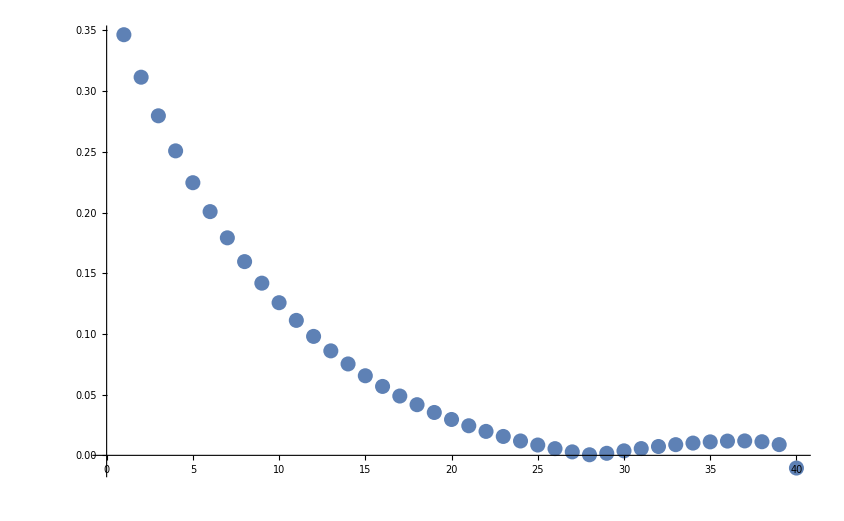

```mathematica
ListPlot[Table[Det[cJηext@@Join[ϕlist[[ii]],legvals[[ii]]]],{ii,50,89}]//Chop]
```

```mathematica
Det[cJηext@@Join[(parampath/.alphasol[[1]]),iksolC[parampath/.alphasol[[1]]]]]
```

0.0542931-5.15131×10^-17 ⅈ

```mathematica
cηext@@Join[(parampath/.alphasol[[1]]),iksolC[parampath/.alphasol[[1]]]]//Norm
```

5.35214×10^-16

```mathematica
MatrixRank[cJηext@@Join[(parampath/.alphasol[[1]]),iksolC[parampath/.alphasol[[1]]]]]
```

18

```mathematica
solzsingular=Solve[(g11/.{x->0,y->0})==0,z]
```

{{z→-0.525465},{z→0.0625327},{z→0.323866}}

```mathematica
g11/.Inner[Rule,{x,y,z},{0,0,z/.solzsingular[[3]]},List]
```

-1.73472×10^-18

```mathematica
cJηext@@Join[({x,y,z,0.2,0,0}/.Inner[Rule,{x,y,z},{0,0,z/.solzsingular[[3]]},List]),iksolC[({x,y,z,0.2,0,0}/.Inner[Rule,{x,y,z},{0,0,z/.solzsingular[[3]]},List])]]//Det
```

0.0000905164-3.7085×10^-19 ⅈ

```mathematica
xlist//Chop//MatrixForm
```

(0.2 | 0 | 1.28 | 0.2 | 0 | 0
0.189528 | 0.010472 | 1.26953 | 0.2 | 0 | 0
0.179056 | 0.020944 | 1.25906 | 0.2 | 0 | 0
0.168584 | 0.0314159 | 1.24858 | 0.2 | 0 | 0
0.158112 | 0.0418879 | 1.23811 | 0.2 | 0 | 0
0.14764 | 0.0523599 | 1.22764 | 0.2 | 0 | 0
0.137168 | 0.0628319 | 1.21717 | 0.2 | 0 | 0
0.126696 | 0.0733038 | 1.2067 | 0.2 | 0 | 0
0.116224 | 0.0837758 | 1.19622 | 0.2 | 0 | 0
0.105752 | 0.0942478 | 1.18575 | 0.2 | 0 | 0
0.0952802 | 0.10472 | 1.17528 | 0.2 | 0 | 0
0.0848083 | 0.115192 | 1.16481 | 0.2 | 0 | 0
0.0743363 | 0.125664 | 1.15434 | 0.2 | 0 | 0
0.0638643 | 0.136136 | 1.14386 | 0.2 | 0 | 0
0.0533923 | 0.146608 | 1.13339 | 0.2 | 0 | 0
0.0429204 | 0.15708 | 1.12292 | 0.2 | 0 | 0
0.0324484 | 0.167552 | 1.11245 | 0.2 | 0 | 0
0.0219764 | 0.178024 | 1.10198 | 0.2 | 0 | 0
0.0115044 | 0.188496 | 1.0915 | 0.2 | 0 | 0
0.00103247 | 0.198968 | 1.08103 | 0.2 | 0 | 0
-0.00943951 | 0.20944 | 1.07056 | 0.2 | 0 | 0
-0.0199115 | 0.219911 | 1.06009 | 0.2 | 0 | 0
-0.0303835 | 0.230383 | 1.04962 | 0.2 | 0 | 0
-0.0408554 | 0.240855 | 1.03914 | 0.2 | 0 | 0
-0.0513274 | 0.251327 | 1.02867 | 0.2 | 0 | 0
-0.0617994 | 0.261799 | 1.0182 | 0.2 | 0 | 0
-0.0722714 | 0.272271 | 1.00773 | 0.2 | 0 | 0
-0.0827433 | 0.282743 | 0.997257 | 0.2 | 0 | 0
-0.0932153 | 0.293215 | 0.986785 | 0.2 | 0 | 0
-0.103687 | 0.303687 | 0.976313 | 0.2 | 0 | 0
-0.114159 | 0.314159 | 0.965841 | 0.2 | 0 | 0
-0.124631 | 0.324631 | 0.955369 | 0.2 | 0 | 0
-0.135103 | 0.335103 | 0.944897 | 0.2 | 0 | 0
-0.145575 | 0.345575 | 0.934425 | 0.2 | 0 | 0
-0.156047 | 0.356047 | 0.923953 | 0.2 | 0 | 0
-0.166519 | 0.366519 | 0.913481 | 0.2 | 0 | 0
-0.176991 | 0.376991 | 0.903009 | 0.2 | 0 | 0
-0.187463 | 0.387463 | 0.892537 | 0.2 | 0 | 0
-0.197935 | 0.397935 | 0.882065 | 0.2 | 0 | 0
-0.208407 | 0.408407 | 0.871593 | 0.2 | 0 | 0
-0.218879 | 0.418879 | 0.861121 | 0.2 | 0 | 0
-0.229351 | 0.429351 | 0.850649 | 0.2 | 0 | 0
-0.239823 | 0.439823 | 0.840177 | 0.2 | 0 | 0
-0.250295 | 0.450295 | 0.829705 | 0.2 | 0 | 0
-0.260767 | 0.460767 | 0.819233 | 0.2 | 0 | 0
-0.271239 | 0.471239 | 0.808761 | 0.2 | 0 | 0
-0.281711 | 0.481711 | 0.798289 | 0.2 | 0 | 0
-0.292183 | 0.492183 | 0.787817 | 0.2 | 0 | 0
-0.302655 | 0.502655 | 0.777345 | 0.2 | 0 | 0
-0.313127 | 0.513127 | 0.766873 | 0.2 | 0 | 0
-0.323599 | 0.523599 | 0.756401 | 0.2 | 0 | 0
-0.334071 | 0.534071 | 0.745929 | 0.2 | 0 | 0
-0.344543 | 0.544543 | 0.735457 | 0.2 | 0 | 0
-0.355015 | 0.555015 | 0.724985 | 0.2 | 0 | 0
-0.365487 | 0.565487 | 0.714513 | 0.2 | 0 | 0
-0.375959 | 0.575959 | 0.704041 | 0.2 | 0 | 0
-0.386431 | 0.586431 | 0.693569 | 0.2 | 0 | 0
-0.396903 | 0.596903 | 0.683097 | 0.2 | 0 | 0
-0.407375 | 0.607375 | 0.672625 | 0.2 | 0 | 0
-0.417847 | 0.617847 | 0.662153 | 0.2 | 0 | 0
-0.428319 | 0.628319 | 0.651681 | 0.2 | 0 | 0
-0.438791 | 0.638791 | 0.641209 | 0.2 | 0 | 0
-0.449262 | 0.649262 | 0.630738 | 0.2 | 0 | 0
-0.459734 | 0.659734 | 0.620266 | 0.2 | 0 | 0
-0.470206 | 0.670206 | 0.609794 | 0.2 | 0 | 0
-0.480678 | 0.680678 | 0.599322 | 0.2 | 0 | 0
-0.49115 | 0.69115 | 0.58885 | 0.2 | 0 | 0
-0.501622 | 0.701622 | 0.578378 | 0.2 | 0 | 0
-0.512094 | 0.712094 | 0.567906 | 0.2 | 0 | 0
-0.522566 | 0.722566 | 0.557434 | 0.2 | 2.14691×10^-10 | 0
-0.533038 | 0.733038 | 0.546962 | 0.2 | 0 | 0
-0.54351 | 0.74351 | 0.53649 | 0.2 | 0 | 0
-0.553982 | 0.753982 | 0.526018 | 0.2 | 0 | 0
-0.564454 | 0.764454 | 0.515546 | 0.2 | 0 | 0
-0.574926 | 0.774926 | 0.505074 | 0.2 | 0 | 0
-0.585398 | 0.785398 | 0.494602 | 0.2 | 0 | 0
-0.59587 | 0.79587 | 0.48413 | 0.2 | 1.7019×10^-9 | 0
-0.609227 | 0.804462 | 0.475134 | 0.195252 | 0.00302648 | 0
-0.623362 | 0.812575 | 0.466405 | 0.189159 | 0.00703003 | 0
-0.637494 | 0.820719 | 0.45751 | 0.183004 | 0.0112331 | 0
-0.651631 | 0.828885 | 0.448431 | 0.176782 | 0.0156777 | 0
-0.665787 | 0.837063 | 0.439147 | 0.170485 | 0.0204214 | 0
-0.679983 | 0.84523 | 0.429633 | 0.164105 | 0.0255458 | 0
-0.69425 | 0.853357 | 0.419857 | 0.157627 | 0.0311728 | 0
-0.708644 | 0.861387 | 0.409778 | 0.151033 | 0.0374978 | 0
-0.723265 | 0.869217 | 0.399336 | 0.144287 | 0.0448684 | 0
-0.738338 | 0.876617 | 0.388431 | 0.13732 | 0.0540185 | 0
-0.754579 | 0.882846 | 0.376815 | 0.129912 | 0.0671788 | 0
-0.781305 | 0.878265 | 0.361869 | 0.119136 | 0.112026 | 5.29347×10^-6)